```mathematica
Get["Minimal.wl",Path->NotebookDirectory[]]
SetOptions[Contract,Dimension-> d]
{Dimension->d,Vectors->Automatic,Indices->All};
```

{Dimension→d,Vectors→Automatic,Indices→All}

## Initialization

#### Formatting

```mathematica
Format[Cor[exp_]]:=⟨exp⟩
Format[Cor[exp_,exp2_]]:=Subscript[⟨exp⟩, exp2]
Format[e[i_,j_,k_]]:= Superscript[ϵ,{i,j,k}];

CorrFormat={o[i_]o[j_]o[k_]o[l_]->Cor[o[i]o[j]o[k]o[l]],Subscript[T, μ_ ν_][i_]o[j_]o[k_]o[l_]->Cor[Subscript[T, μ ν][i]o[j]o[k]o[l]],Subscript[J, μ_ ν_ σ_ ρ_][i_]o[j_]o[k_]o[l_]->Cor[Subscript[J, μ ν σ ρ][i]o[j]o[k]o[l]],o[i_]o[j_]Subscript[J, α_][k_]Subscript[J, β_][l_]->Cor[o[i]o[j]Subscript[J, α][k]Subscript[J, β][l]],Subscript[J, α_][i_]Subscript[J, β_][j_]Subscript[J, γ_][k_]Subscript[J, σ_][l_]->Cor[Subscript[J, α][i]Subscript[J, β][j]Subscript[J, γ][k]Subscript[J, σ][l]],Subscript[J, α_][i_]Subscript[J, β_][j_]o[k_]Subscript[T, μ_ ν_][l_]->Cor[Subscript[J, α][i]Subscript[J, β][j]o[k]Subscript[T, μ ν][l]],
Subscript[T, μ_ ν_][i_]Subscript[T, α_ β_][j_]Subscript[T, γ_ δ_][k_]Subscript[T, σ_ ρ_][l_]->Cor[Subscript[T, μ ν][i]Subscript[T, α β][j]Subscript[T, γ δ][k]Subscript[T, σ ρ][l]],Subscript[T, μ_ ν_][i_]Subscript[T, α_ β_][j_]Subscript[T, γ_ δ_][k_]o[l_]->Cor[Subscript[T, μ ν][i]Subscript[T, α β][j]Subscript[T, γ δ][k]o[l]],Subscript[T, μ_ ν_][i_]Subscript[T, α_ β_][j_]o[k_]o[l_]->Cor[Subscript[T, μ ν][i]Subscript[T, α β][j]o[k]o[l]],Subscript[J, μ_ ν_ σ_ ρ_][i_]Subscript[T, α_ β_][j_]Subscript[T, γ_ δ_][k_]o[l_]->Cor[Subscript[J, μ ν σ ρ][i]Subscript[T, α β][j]Subscript[T, γ δ][k]o[l]]};

CorrFormat2={Subscript[T, m_^2][i_]Subscript[T, m_^2][j_]Subscript[T, m_^2][k_]Subscript[T, m_^2][l_]->Cor[Subscript[T, m m][i]Subscript[T, m m][j]Subscript[T, m m][k]Subscript[T, m m][l]],Subscript[T, μ_ ν_][i_]Subscript[T, α_ β_][j_]Subscript[T, γ_ δ_][k_]o[l_]->Cor[Subscript[T, μ ν][i]Subscript[T, α β][j]Subscript[T, γ δ][k]o[l]]};
```

#### Symmetrization Functions

```mathematica
Sym[expr_,μ_,ν_,ρ_]:=(expr+(expr/.{ρ->ν, ν->ρ})+(expr/.{μ->ν, ν->μ })+(expr/.{μ->ρ, ρ->μ })+(expr/.{μ->ν, ν->ρ, ρ->μ})+(expr/.{μ->ρ, ρ->ν,ν->μ }))/6

Sym[expr_,μ_,ν_]:=(expr+(expr/.{μ->ν, ν->μ }))/2
```

#### Epsilon contractions

```mathematica
PermuteEpsilon=Dispatch[{e[i_,j_,k_] :> Signature[e[i,j,k]]*Sort[e[i,j,k]]}];

epsx={e[x_,a_+b_,z_]->e[x,a,z]+e[x,b,z],e[x_,y_,a_+b_]->e[x,y,a]+e[x,y,b]};
epsx2={e[x_,x_,z_]->0,e[x_,z_,x_]->0,e[z_,x_,x_]->0,e[x_,x_,x_]->0};
epsx3={e[-x_,y_,z_]->-e[x,y,z],e[x_,-y_,z_]->-e[x,y,z],e[x_,y_,-z_]->-e[x,y,z]};

epsprod={e[i_,j_,k_]e[l_,m_,n_]->(δ[i,l](δ[j,m]δ[k,n]-δ[j,n]δ[k,m])-δ[i,m](δ[j,l]δ[k,n]-δ[j,n]δ[k,l])+δ[i,n](δ[j,l]δ[k,m]-δ[j,m]δ[k,l]))};

epsprod2={e[i_,j_,k_]e[i_,m_,n_]->δ[j,m]δ[k,n]-δ[k,m]δ[j,n],e[i_,j_,k_]e[m_,n_,i_]->δ[j,m]δ[k,n]-δ[k,m]δ[j,n],
e[i_,j_,k_]e[m_,i_,n_]->-δ[j,m]δ[k,n]+δ[k,m]δ[j,n],e[k_,i_,j_]e[n_,i_,m_]->δ[j,m]δ[k,n]-δ[k,m]δ[j,n],e[k_,i_,j_]e[m_,n_,i_]->δ[j,m]δ[k,n]-δ[k,m]δ[j,n]};

epscont={e[a_,b_,c_] p[i_][a_]->e[p[i],b,c],e[a_,b_,c_] p[i_][b_]->e[a,p[i],c],e[a_,b_,c_] p[i_][c_]->e[a,b,p[i]]};
```

#### Momentum identities

```mathematica
permuteip={p[2]·p[1]->p[1]·p[2],p[3]·p[1]->p[1]·p[3],p[3]·p[2]->p[2]·p[3],p[1]·p[1]->p[1]^2,p[2]·p[2]->p[2]^2,p[3]·p[3]->p[3]^2};
ipreplace3={p[1]·p[3]->(p[2]^2-p[1]^2-p[3]^2)/2,p[1]·p[2]->(p[3]^2-p[1]^2-p[2]^2)/2,p[2]·p[3]->(p[1]^2-p[2]^2-p[3]^2)/2};
ipreplace4={p[i_]·p[4]->-(p[i]·p[1]+p[i]·p[2]+p[i]·p[3]),p[4]^2->(p[1]^2+p[2]^2+p[3]^2+2(p[1]·p[2]+p[2]·p[3]+p[1]·p[3]))};
momcons3={p[3][μ_]->-p[1][μ]-p[2][μ]};
momcons4={p[4][μ_]->-p[1][μ]-p[2][μ]-p[3][μ]};
```

#### Spinor helicity

```mathematica
Format[z[i_][p]]:= Subsuperscript[z,i,"+"];
Format[z[i_][m]]:= Subsuperscript[z,i,"-"];
Format[z[i_][p][μ_]]:=Subscript[ Subsuperscript[z, i,μ],"+"];
Format[z[i_][m][μ_]]:=Subscript[ Subsuperscript[z, i,μ],"-"];

Zcontract= Dispatch[{p[i_][j_]z[k_][c_][j_]:> p[i].z[k][c],q_[j_]z[k_][c_][j_]:> q.z[k][c],δ[i_,j_]z[k_][c_][i_]:> z[k][c][j],z[i_][c_][j_]^2->0 ,p[i_].z[i_][c_]:> 0,z[i_][c1_][j_]z[k_][c2_][j_]:> z[i][c1].z[k][c2]}];

sph={p[i_].z[j_][m]:>-a[j,i,b] a[j,i]/(4 p[j]),p[i_].z[j_][p]:>a[i,j,b] a[j,b,i,b]/(4 p[j]),
z[i_][m].z[j_][m]:>-a[i,j]^2/(8 p[i] p[j]),z[i_][p].z[j_][p]:>-a[i,b,j,b]^2/(8 p[i] p[j]),
z[i_][p].z[j_][m]:>-a[j,i,b]^2/(8 p[i] p[j])};

permutesph={a[2,1]->-a[1,2],a[3,1]->-a[1,3],a[3,2]->-a[2,3],a[2,b,1,b]->-a[1,b,2,b],a[3,b,1,b]->-a[1,b,3,b],a[3,b,2,b]->-a[2,b,3,b],a[1,1]->0,a[2,2]->0,a[3,3]->0,a[1,b,1,b]->0,a[2,b,2,b]->0,a[3,b,3,b]->0,a[1,1,b]->-2 p[1],a[2,2,b]->-2 p[2],a[3,3,b]->-2 p[3]};
```

#### Projection operators and magnitude function

```mathematica
pi[n_][i_,j_] := δ[i,j] - p[n][i] p[n][j] / p[n]^2;
PI[d_][n_][i_,j_,k_,l_]:=1/2( pi[n][i,k]pi[n][j,l]+pi[n][i,l]pi[n][j,k]) - 1/(d-1) pi[n][i,j] pi[n][k,l];

Sigma[i_,j_][μ_,ν_,α_,β_]:=p[i][c]e[μ,c,α]p[j][d]e[ν,d,β];
zeta[i_,j_][μ_,ν_,α_,β_]:=pi[i][μ,α]pi[j][ν,β];

Δ[μ_,ν_,α_,β_][r_]:=e[μ,θ,α]p[r][θ]pi[r][ν,β]+e[ν,θ,α]p[r][θ]pi[r][μ,β]+e[μ,θ,β]p[r][θ]pi[r][ν,α]+e[ν,θ,β]p[r][θ]pi[r][μ,α];
zetaodd[i_,j_][μ_,ν_,α_,β_]:=e[μ,a1,b]p[i][a1]pi[i][b,α]e[ν,b1,a]p[i][b1]pi[j][a,β]

Mf[exp_]:=If[Length[exp/.{-p[m_]->p[m]}]==1 ,exp/.{-p[m_]->p[m]},
Sqrt[Contract[Sum[exp[[j]][α]/.{(-p[m_])[α]->-p[m][α]},{j,Length[exp]}]Sum[exp[[j]][α]/.{(-p[m_])[α]->-p[m][α]},{j,Length[exp]}]]]
]
```

#### Misc

```mathematica
ffid={Subscript[X0, a_ b_ c_ d_ e_ f_ g_ h_] δ[a_,i_]->Subscript[X0, i b c d e f g h],Subscript[X1, a_ b_ c_ d_ e_ f_ g_ h_] δ[a_,i_]->Subscript[X1, i b c d e f g h],Subscript[X2, a_ b_ c_ d_ e_ f_ g_ h_] δ[a_,i_]->Subscript[X2, i b c d e f g h],
Subscript[X3, a_ b_ c_ d_ e_ f_ g_ h_] δ[a_,i_]->Subscript[X3, i b c d e f g h],Subscript[X4, a_ b_ c_ d_ e_ f_ g_ h_] δ[a_,i_]->Subscript[X4, i b c d e f g h],
Subscript[X0, α1 α2 α3 β1 β2 β3 ν_ ρ_] p[4][ν_]->0,Subscript[X1, α1 α2 α3 β1 β2 β3 ν_ ρ_] p[4][ν_]->0,Subscript[X2, α1 α2 α3 β1 β2 β3 ν_ ρ_] p[4][ν_]->0,Subscript[X3, α1 α2 α3 β1 β2 β3 ν_ ρ_] p[4][ν_]->0,Subscript[X4, α1 α2 α3 β1 β2 β3 ν_ ρ_] p[4][ν_]->0};

PE={X3->X1,Subscript[X2, a_ b_ c_ d_ e_ f_ g_ h_]->Subscript[X0, a b c d e f g h]+Subscript[X4, a b c d e f g h]};

ffreplace=
{E1[4,1,2,3]->E1A,E1[3,1,2,4]->E1B,
E2[4,1,2,3]->E2A,E2[3,1,2,4]->E2B,
E3[4,1,2,3]->E3A,E3[3,1,2,4]->E3B,
E4[4,1,2,3]->E4A,E4[3,1,2,4]->E4B,
E5[4,1,2,3]->E5A,E5[3,1,2,4]->E5B,
E6[4,1,2,3]->E6A,E6[3,1,2,4]->E6B,
E7[4,1,2,3]->E7A,E7[3,1,2,4]->E7B,
E8[4,1,2,3]->E8A,E8[3,1,2,4]->E8B,
E9[4,1,2,3]->E9A,E9[3,1,2,4]->E9B,
E10[4,1,2,3]->E10A,E10[3,1,2,4]->E10B,
E11[4,1,2,3]->E11A,E11[3,1,2,4]->E11B,
E12[4,1,2,3]->E12A,E12[3,1,2,4]->E12B,
E13[4,1,2,3]->E13A,E13[3,1,2,4]->E13B,
E14[4,1,2,3]->E14A,E14[3,1,2,4]->E14B,
E15[4,1,2,3]->E15A,E15[3,1,2,4]->E15B,
E16[4,1,2,3]->E16A,E16[3,1,2,4]->E16B,

O1[4,1,2,3]->O1A,O1[3,1,2,4]->O1B,
O2[4,1,2,3]->O2A,O2[3,1,2,4]->O2B,
O3[4,1,2,3]->O3A,O3[3,1,2,4]->O3B,
O4[4,1,2,3]->O4A,O4[3,1,2,4]->O4B,
O5[4,1,2,3]->O5A,O5[3,1,2,4]->O5B,
O6[4,1,2,3]->O6A,O6[3,1,2,4]->O6B,
O7[4,1,2,3]->O7A,O7[3,1,2,4]->O7B,
O8[4,1,2,3]->O8A,O8[3,1,2,4]->O8B,
O9[4,1,2,3]->O9A,O9[3,1,2,4]->O9B,
O10[4,1,2,3]->O10A,O10[3,1,2,4]->O10B,
O11[4,1,2,3]->O11A,O11[3,1,2,4]->O11B,
O12[4,1,2,3]->O12A,O12[3,1,2,4]->O12B,
O13[4,1,2,3]->O13A,O13[3,1,2,4]->O13B,
O14[4,1,2,3]->O14A,O14[3,1,2,4]->O14B,
O15[4,1,2,3]->O15A,O15[3,1,2,4]->O15B,
O16[4,1,2,3]->O16A,O16[3,1,2,4]->O16B};

ffrelations={}

Den=(e[i,j,k]p[1][i]p[2][j]p[3][k]e[l,m,n]p[1][l]p[2][m]p[3][n]/.epsprod//Contract)
```

{}

2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2

## Ansatzes

### Even

```mathematica
TJJOeven[i_,j_,k_,l_,μ_,ν_,α_,β_]:=PI[4][i][μ,ν,a1,b1]pi[j][α,c1]pi[k][β,d1](
E1[i,j,k,l]p[j][a1]p[j][b1]p[i][c1]p[i][d1]
+E2[i,j,k,l]p[k][a1]p[j][b1]p[i][c1]p[i][d1]
+E3[i,j,k,l]p[j][a1]p[k][b1]p[i][c1]p[i][d1]
+E4[i,j,k,l]p[k][a1]p[k][b1]p[i][c1]p[i][d1]
+E5[i,j,k,l]p[j][a1]p[j][b1]p[k][c1]p[i][d1]
+E6[i,j,k,l]p[k][a1]p[j][b1]p[k][c1]p[i][d1]
+E7[i,j,k,l]p[j][a1]p[k][b1]p[k][c1]p[i][d1]
+E8[i,j,k,l]p[k][a1]p[k][b1]p[k][c1]p[i][d1]
+E9[i,j,k,l]p[j][a1]p[j][b1]p[i][c1]p[j][d1]
+E10[i,j,k,l]p[k][a1]p[j][b1]p[i][c1]p[j][d1]
+E11[i,j,k,l]p[j][a1]p[k][b1]p[i][c1]p[j][d1]
+E12[i,j,k,l]p[k][a1]p[k][b1]p[i][c1]p[j][d1]
+E13[i,j,k,l]p[j][a1]p[j][b1]p[k][c1]p[j][d1]
+E14[i,j,k,l]p[k][a1]p[j][b1]p[k][c1]p[j][d1]
+E15[i,j,k,l]p[j][a1]p[k][b1]p[k][c1]p[j][d1]
+E16[i,j,k,l]p[k][a1]p[k][b1]p[k][c1]p[j][d1])
```

```mathematica
ExchangeTest=(((TJJOeven[1,3,2,4,μ,ν,β,α]/.{B1[1,3,2,4]->B1[1,2,3,4],C1[1,3,2,4]->C1[1,2,3,4],A1[1,3,2,4]->D1[1,2,3,4],D1[1,3,2,4]->A1[1,2,3,4],J1[1,3,2,4]->H1[1,2,3,4],N1[1,3,2,4]->E1[1,2,3,4],E1[1,3,2,4]->N1[1,2,3,4],O1[1,3,2,4]->R1[1,2,3,4],R1[1,3,2,4]->O1[1,2,3,4],H1[1,3,2,4]->J1[1,2,3,4]}/.{P1[1,3,2,4]->P1[1,2,3,4]+Q1[1,2,3,4]-Q1[1,3,2,4],L1[1,3,2,4]->F1[1,2,3,4]+G1[1,2,3,4]-M1[1,3,2,4],F1[1,3,2,4]->L1[1,2,3,4]+M1[1,2,3,4]-G1[1,3,2,4]})-(TJJOeven[1,2,3,4,μ,ν,α,β]))//Contract)/.d->3//Simplify
```

0

### Odd

```mathematica
TJJOodd[i_,j_,k_,l_,μ_,ν_,α_,β_]:=(Δ[μ,ν,a1,b1][i]pi[j][α,c1]pi[k][β,d1]+PI[4][i][μ,ν,a1,b1](e[α,b3,c1]p[j][b3])/p[j] pi[k][β,d1]+PI[4][i][μ,ν,a1,b1]pi[j][α,c1](e[β,a3,d1]p[k][a3])/p[k])(
O1[i,j,k,l]p[j][a1]p[j][b1]p[i][c1]p[i][d1]
+O2[i,j,k,l]p[k][a1]p[j][b1]p[i][c1]p[i][d1]
+O3[i,j,k,l]p[j][a1]p[k][b1]p[i][c1]p[i][d1]
+O4[i,j,k,l]p[k][a1]p[k][b1]p[i][c1]p[i][d1]
+O5[i,j,k,l]p[j][a1]p[j][b1]p[k][c1]p[i][d1]
+O6[i,j,k,l]p[k][a1]p[j][b1]p[k][c1]p[i][d1]
+O7[i,j,k,l]p[j][a1]p[k][b1]p[k][c1]p[i][d1]
+O8[i,j,k,l]p[k][a1]p[k][b1]p[k][c1]p[i][d1]
+O9[i,j,k,l]p[j][a1]p[j][b1]p[i][c1]p[j][d1]
+O10[i,j,k,l]p[k][a1]p[j][b1]p[i][c1]p[j][d1]
+O11[i,j,k,l]p[j][a1]p[k][b1]p[i][c1]p[j][d1]
+O12[i,j,k,l]p[k][a1]p[k][b1]p[i][c1]p[j][d1]
+O13[i,j,k,l]p[j][a1]p[j][b1]p[k][c1]p[j][d1]
+O14[i,j,k,l]p[k][a1]p[j][b1]p[k][c1]p[j][d1]
+O15[i,j,k,l]p[j][a1]p[k][b1]p[k][c1]p[j][d1]
+O16[i,j,k,l]p[k][a1]p[k][b1]p[k][c1]p[j][d1])
```

```mathematica
ExchangeTestOdd=((TJJOodd[1,2,3,4,μ,ν,α,β]-(TJJOodd[1,3,2,4,μ,ν,β,α]/.{A2[1,3,2,4]->D2[1,2,3,4],E2[1,3,2,4]->N2[1,2,3,4],B2[1,3,2,4]->B2[1,2,3,4],C2[1,3,2,4]->C2[1,2,3,4],D2[1,3,2,4]->A2[1,2,3,4],H2[1,3,2,4]->J2[1,2,3,4],J2[1,3,2,4]->H2[1,2,3,4],N2[1,3,2,4]->E2[1,2,3,4],O2[1,3,2,4]->R2[1,2,3,4],R2[1,3,2,4]->O2[1,2,3,4]}/.{F2[1,3,2,4]->L2[1,2,3,4]+M2[1,2,3,4]-G2[1,3,2,4],L2[1,3,2,4]->F2[1,2,3,4]+G2[1,2,3,4]-M2[1,3,2,4],P2[1,3,2,4]->P2[1,2,3,4]+Q2[1,2,3,4]-Q2[1,3,2,4]}))//Contract)//.epscont/.PermuteEpsilon
```

0

## Pole Equations

```mathematica
(*P1RTest1[i_,j_,k_,l_]:=- e0 Cor[o[p[k]] o[p[l]] Subscript[J, b][p[i]] Subscript[J, β][p[j]],odd] Cor[Subscript[J, α][p[i]] Subscript[J, ρ][-p[i]],FF] e[b,ν,p[i]] p[i][μ]+A e0 Cor[o[p[k]] o[p[l]] Subscript[J, b][p[i]] Subscript[J, β][p[j]],CB] Cor[Subscript[J, α][p[i]] Subscript[J, ρ][-p[i]],odd]e[b,ν,p[i]] p[i][μ];*)
```

```mathematica
(*Add <JJOO> part later*)
```

```mathematica
PE1Lterm[i_,j_,k_,l_,μ_,ν_,ρ_,α_,β_]:=Sym[-I r0 p[k]p[k][μ]TJJOeven[k,i,j,l,ν,ρ,α,β]  ,μ,ν,ρ];
PE1Rterm[i_,j_,k_,l_,μ_,ν_,ρ_,α_,β_]:=Sym[c2  e[ν,a,b] p[k][a]p[k][μ] TJJOodd[k,i,j,l,b,ρ,α,β],μ,ν,ρ];

PE2Lterm[i_,j_,k_,l_,μ_,ν_,ρ_,α_,β_]:=Sym[c2 e[ν,a,b] p[k][a]p[k][μ]TJJOeven[k,i,j,l,b,ρ,α,β] ,μ,ν,ρ];
PE2Rterm[i_,j_,k_,l_,μ_,ν_,ρ_,α_,β_]:= Sym[I r0 p[k]p[k][μ]TJJOodd[k,i,j,l,ν,ρ,α,β],μ,ν,ρ];

PE1term[i_,j_,k_,l_,μ_,ν_,ρ_,α_,β_]:=PE1Lterm[i,j,k,l,μ,ν,ρ,α,β]-PE1Rterm[i,j,k,l,μ,ν,ρ,α,β];
PE2term[i_,j_,k_,l_,μ_,ν_,ρ_,α_,β_]:=PE2Lterm[i,j,k,l,μ,ν,ρ,α,β]-PE2Rterm[i,j,k,l,μ,ν,ρ,α,β];
```

```mathematica
PE1L=((PE1Lterm[1,2,3,4,μ,ν,ρ,α,β]+PE1Lterm[1,2,4,3,μ,ν,ρ,α,β]//Expand)//Contract)/.ffreplace
```

(ⅈ E13B r0 p_1·p_2 (p_1·p_3)^2 δ_(ν,ρ) p_1^α p_1^β p_3^μ)/(9 p_1^2 p_3)+(ⅈ E9B r0 (p_1·p_3)^3 δ_(ν,ρ) p_1^α p_1^β p_3^μ)/(9 p_1^2 p_3)+(ⅈ E14B r0 p_1·p_2 p_1·p_3 p_2·p_3 δ_(ν,ρ) p_1^α p_1^β p_3^μ)/(9 p_1^2 p_3)+(ⅈ E15B r0 p_1·p_2 p_1·p_3 p_2·p_3 δ_(ν,ρ) p_1^α p_1^β p_3^μ)/(9 p_1^2 p_3)+(ⅈ E10B r0 (p_1·p_3)^2 p_2·p_3 δ_(ν,ρ) p_1^α p_1^β p_3^μ)/(9 p_1^2 p_3)+(ⅈ E11B r0 (1)^2 p_2·p_3 δ_1 p_1^α p_1^β p_3^μ)/(9 p_1^2 p_3)+(ⅈ 8)/1+3257
 |  |  |  |

```mathematica
PE1R=((PE1Rterm[1,2,3,4,μ,ν,ρ,α,β]+PE1Rterm[1,2,4,3,μ,ν,ρ,α,β]//Expand)/.ffreplace/.epsprod2/.epsprod//Contract)
```

(2 c2 O13B p_1·p_2 (p_1·p_3)^2 δ_(ν,ρ) p_1^α p_1^β p_3^μ)/(3 p_1^2)+(2 c2 O9B (p_1·p_3)^3 δ_(ν,ρ) p_1^α p_1^β p_3^μ)/(3 p_1^2)+(2 c2 O14B p_1·p_2 p_1·p_3 p_2·p_3 δ_(ν,ρ) p_1^α p_1^β p_3^μ)/(3 p_1^2)+(2 c2 O15B p_1·p_2 p_1·p_3 p_2·p_3 δ_(ν,ρ) p_1^α p_1^β p_3^μ)/(3 p_1^2)+(2 c2 O10B (p_1·p_3)^2 p_2·p_3 δ_(ν,ρ) p_1^α p_1^β p_3^μ)/(3 p_1^2)+(2 c2 O11B (1)^2 p_2·p_3 δ_1 p_1^α p_1^β p_3^μ)/(3 p_1^2)+(2 7 p_3^μ)/(3 p_1^2)+14705
 |  |  |  |

```mathematica
PE2L=((e[l,m,n]p[1][l]p[2][m]p[3][n])((PE2Lterm[1,2,3,4,μ,ν,ρ,α,β]+PE2Lterm[1,2,4,3,μ,ν,ρ,α,β]//Expand)/.ffreplace//Contract)//Expand)/.epsprod//Contract
```

-(c2 E13B p_1·p_2 p_1·p_3 p_2·p_3 p_1^α p_1^β p_1^ν p_1^ρ p_3^μ)/(3 p_1^2)-(c2 E9B (p_1·p_3)^2 p_2·p_3 p_1^α p_1^β p_1^ν p_1^ρ p_3^μ)/(3 p_1^2)-(c2 E14B p_1·p_2 (p_2·p_3)^2 p_1^α p_1^β p_1^ν p_1^ρ p_3^μ)/(6 p_1^2)-(c2 E15B p_1·p_2 (p_2·p_3)^2 p_1^α p_1^β p_1^ν p_1^ρ p_3^μ)/(6 p_1^2)-(c2 E10B p_1·p_3 (p_2·p_3)^2 p_1^α p_1^β p_1^ν p_1^ρ p_3^μ)/(6 p_1^2)-(c2 E11B p_1·p_3 1^2 p_1^α p_1^β p_1^ν p_1^ρ p_3^μ)/(6 p_1^2)+1/(3 1)+8953+1+(c2 E1A 6 p_4^ν p_4^ρ)/(3 p_4^2)+(c2 E2A (p_2·p_4)^2 p_1^2 p_3^μ p_4^α p_4^β p_4^ν p_4^ρ)/(6 p_4^2)+(c2 E3A (p_2·p_4)^2 p_1^2 p_3^μ p_4^α p_4^β p_4^ν p_4^ρ)/(6 p_4^2)-(c2 E2A (p_1·p_4)^2 p_2^2 p_3^μ p_4^α p_4^β p_4^ν p_4^ρ)/(6 p_4^2)-(c2 E3A (p_1·p_4)^2 p_2^2 p_3^μ p_4^α p_4^β p_4^ν p_4^ρ)/(6 p_4^2)-(c2 E4A p_1·p_4 p_2·p_4 p_2^2 p_3^μ p_4^α p_4^β p_4^ν p_4^ρ)/(3 p_4^2)
 |  |  |  |

```mathematica
PE2R=((e[l,m,n]p[1][l]p[2][m]p[3][n])((PE2Rterm[1,2,3,4,μ,ν,ρ,α,β]+PE2Rterm[1,2,4,3,μ,ν,ρ,α,β]//Expand)/.ffreplace//Contract)//Expand)/.epsprod//Contract
```

(ⅈ O13B r0 p_1·p_2 (p_1·p_3)^2 p_2·p_3 δ_(ν,ρ) p_1^α p_1^β p_3^μ)/(9 p_1 p_3)-(ⅈ O9B r0 (p_1·p_3)^3 p_2·p_3 δ_(ν,ρ) p_1^α p_1^β p_3^μ)/(9 p_1 p_3)+(ⅈ O14B r0 p_1·p_2 p_1·p_3 (p_2·p_3)^2 δ_(ν,ρ) p_1^α p_1^β p_3^μ)/(9 p_1 p_3)+28407+(ⅈ O6A r0 p_1·p_2 p_1 p_2^2 p_3^α p_4^β p_4^μ p_4^ν p_4^ρ)/(3 p_4)+(ⅈ O7A r0 p_1·p_2 p_1 p_2^2 p_3^α p_4^β p_4^μ p_4^ν p_4^ρ)/(3 p_4)+(ⅈ O4A r0 p_2·p_4 p_1 p_2^2 p_3^α p_4^β p_4^μ p_4^ν p_4^ρ)/(3 p_4)+(ⅈ O5A r0 p_1^3 p_2^2 p_3^α p_4^β p_4^μ p_4^ν p_4^ρ)/(3 p_4)+(ⅈ O8A r0 p_1 p_2^4 p_3^α p_4^β p_4^μ p_4^ν p_4^ρ)/(3 p_4)
 |  |  |  |

```mathematica
TestPE1L=(pi[4][μ,σ]pi[4][ν,γ]pi[4][ρ,η]PE1L//Contract)/.{d->3}/.momcons4//Expand
```

(ⅈ E13B r0 p_1·p_2 (p_1·p_3)^2 p_3·p_4 δ_(η,σ) p_1^α p_1^β p_1^γ)/(9 p_1^2 p_3 p_4^2)+(ⅈ E9B r0 (p_1·p_3)^3 p_3·p_4 δ_(η,σ) p_1^α p_1^β p_1^γ)/(9 p_1^2 p_3 p_4^2)+(ⅈ E14B r0 p_1·p_2 p_1·p_3 p_2·p_3 p_3·p_4 δ_(η,σ) p_1^α p_1^β p_1^γ)/(9 p_1^2 p_3 p_4^2)+(ⅈ E15B r0 p_1·p_2 p_1·p_3 p_2·p_3 p_3·p_4 δ_(η,σ) p_1^α p_1^β p_1^γ)/(9 p_1^2 p_3 p_4^2)+(ⅈ E10B r0 (p_1·p_3)^2 p_2·p_3 p_3·p_4 δ_(η,σ) p_1^α p_1^β p_1^γ)/(9 p_1^2 p_3 p_4^2)+(ⅈ E11B r0 4 p_1^α p_1^β p_1^γ)/(9 p_1^2 p_3 p_4^2)+44250
 |  |  |  |

```mathematica
TestPE1R=(pi[4][μ,σ]pi[4][ν,γ]pi[4][ρ,η]PE1R//Contract)/.{d->3}/.momcons4//Expand
```

(2 c2 O13B p_1·p_2 (p_1·p_3)^2 p_3·p_4 δ_(η,σ) p_1^α p_1^β p_1^γ)/(3 p_1^2 p_4^2)+(2 c2 O9B (p_1·p_3)^3 p_3·p_4 δ_(η,σ) p_1^α p_1^β p_1^γ)/(3 p_1^2 p_4^2)+(2 c2 O14B p_1·p_2 p_1·p_3 p_2·p_3 p_3·p_4 δ_(η,σ) p_1^α p_1^β p_1^γ)/(3 p_1^2 p_4^2)+(2 c2 O15B p_1·p_2 p_1·p_3 p_2·p_3 p_3·p_4 δ_(η,σ) p_1^α p_1^β p_1^γ)/(3 p_1^2 p_4^2)+(2 c2 O10B (p_1·p_3)^2 p_2·p_3 p_3·p_4 δ_(η,σ) p_1^α p_1^β p_1^γ)/(3 p_1^2 p_4^2)+265606+(c2 O8B p_1·p_4 p_2·p_3 p_2^2 p_3^α p_3^β p_3^γ p_3^η p_3^σ)/(p_1 p_3^2 p_4^2)-(2 c2 O2B p_1·p_2 p_3^2 p_3^α p_3^β p_3^γ p_3^η p_3^σ)/p_4^2-(2 c2 O3B p_1·p_2 p_3^2 p_3^α p_3^β p_3^γ p_3^η p_3^σ)/p_4^2-(2 c2 O1B p_1^2 p_3^2 p_3^α p_3^β p_3^γ p_3^η p_3^σ)/p_4^2-(2 c2 O4B p_2^2 p_3^2 p_3^α p_3^β p_3^γ p_3^η p_3^σ)/p_4^2
 |  |  |  |

```mathematica
TestPE2L=(pi[4][μ,σ]pi[4][ν,γ]pi[4][ρ,η]PE2L//Contract)/.{d->3}/.momcons4//Expand
```

(c2 E13B p_1·p_2 p_1·p_4 p_2·p_3 (p_3·p_4)^2 p_1^α p_1^β p_1^γ p_1^η p_1^σ)/p_4^6+(c2 E9B p_1·p_3 p_1·p_4 p_2·p_3 (p_3·p_4)^2 p_1^α p_1^β p_1^γ p_1^η p_1^σ)/p_4^6+(c2 E13B p_1·p_2 p_1·p_3 p_2·p_4 (p_3·p_4)^2 p_1^α p_1^β p_1^γ p_1^η p_1^σ)/p_4^6+(c2 E9B (p_1·p_3)^2 p_2·p_4 (p_3·p_4)^2 p_1^α p_1^β p_1^γ p_1^η p_1^σ)/p_4^6+85093+(3 c2 E3B (p_2·p_3)^2 p_3·p_4 p_1^2 p_3^α p_3^β p_3^γ p_3^η p_3^σ)/(2 p_3^2 p_4^2)-(3 c2 E2B (p_1·p_3)^2 p_3·p_4 p_2^2 p_3^α p_3^β p_3^γ p_3^η p_3^σ)/(2 p_3^2 p_4^2)-(3 c2 E3B (p_1·p_3)^2 p_3·p_4 p_2^2 p_3^α p_3^β p_3^γ p_3^η p_3^σ)/(2 p_3^2 p_4^2)-(3 c2 E4B p_1·p_3 p_2·p_3 p_3·p_4 p_2^2 p_3^α p_3^β p_3^γ p_3^η p_3^σ)/(p_3^2 p_4^2)
 |  |  |  |

```mathematica
TestPE2R=(pi[4][μ,σ]pi[4][ν,γ]pi[4][ρ,η]PE2R//Contract)/.{d->3}/.momcons4//Expand
```

(ⅈ O13B r0 p_1·p_2 (p_1·p_3)^2 p_2·p_3 p_3·p_4 δ_(η,σ) p_1^α p_1^β p_1^γ)/(9 p_1 p_3 p_4^2)-(ⅈ O9B r0 (p_1·p_3)^3 p_2·p_3 p_3·p_4 δ_(η,σ) p_1^α p_1^β p_1^γ)/(9 p_1 p_3 p_4^2)+(ⅈ O14B r0 p_1·p_2 p_1·p_3 (p_2·p_3)^2 p_3·p_4 δ_(η,σ) p_1^α p_1^β p_1^γ)/(9 p_1 p_3 p_4^2)+346598+(ⅈ O5B r0 p_1^3 p_2^2 p_3 p_3^α p_3^β p_3^γ p_3^η p_3^σ)/(3 p_4^2)-(ⅈ O4B r0 p_1·p_3 p_2^3 p_3 p_3^α p_3^β p_3^γ p_3^η p_3^σ)/(3 p_4^2)-(ⅈ O12B r0 p_1^2 p_2^3 p_3 p_3^α p_3^β p_3^γ p_3^η p_3^σ)/(3 p_4^2)+(ⅈ O8B r0 p_1 p_2^4 p_3 p_3^α p_3^β p_3^γ p_3^η p_3^σ)/(3 p_4^2)
 |  |  |  |

```mathematica
PE1=((TestPE1L-TestPE1R)/.{δ[μ_,ν_]->DeltaExp[μ,ν]}//Expand)
```

-(2 c2 O13B p_1·p_2 (p_3·p_4)^3 p_1^α p_1^β p_1^γ p_1^η p_1^σ)/p_4^6-(2 c2 O9B p_1·p_3 (p_3·p_4)^3 p_1^α p_1^β p_1^γ p_1^η p_1^σ)/p_4^6+(8 c2 O13B p_1·p_2 p_1·p_3 p_1·p_4 (p_3·p_4)^2 p_1^α p_1^β p_1^γ p_1^η p_1^σ)/(p_1^2 p_4^6)+639544+(c2 O4B p_2·p_4 p_1^2 p_2^3 p_3^2 p_3^α p_3^β p_3^γ p_3^η p_3^σ)/((2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2) p_4^2)-(2 c2 O4B p_3·p_4 p_1^2 p_2^4 p_3^2 p_3^α p_3^β p_3^γ p_3^η p_3^σ)/((2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2) p_4^2)
 |  |  |  |

```mathematica
PE2=((TestPE2L-TestPE2R)/.{δ[μ_,ν_]->DeltaExp[μ,ν]}//Expand)
```

(c2 E13B p_1·p_2 p_1·p_4 p_2·p_3 (p_3·p_4)^2 p_1^α p_1^β p_1^γ p_1^η p_1^σ)/p_4^6+(c2 E9B p_1·p_3 p_1·p_4 p_2·p_3 (p_3·p_4)^2 p_1^α p_1^β p_1^γ p_1^η p_1^σ)/p_4^6+(c2 E13B p_1·p_2 p_1·p_3 p_2·p_4 (p_3·p_4)^2 p_1^α p_1^β p_1^γ p_1^η p_1^σ)/p_4^6+569036+(ⅈ O8B r0 p_3·p_4 p_1^3 p_2^6 p_3 p_3^α p_3^β p_3^γ p_3^η p_3^σ)/(3 (2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2) p_4^2)
 |  |  |  |

```mathematica
Clear[i,j,k,l,m,n]
```

```mathematica
PE1Test=(PE1/.{p[i_][j_]->p[i,j]}/.set3)/.{p[i_,j_]->p[i][j]}
```

7771+0.953561 c2 O9B p_3^α p_3^β p_3^γ p_3^η p_3^σ+(0.+1.33649 ⅈ) E1B r0 p_3^α p_3^β p_3^γ p_3^η p_3^σ+(0.+0.83432 ⅈ) E2B r0 p_3^α p_3^β p_3^γ p_3^η p_3^σ+(0.+0.83432 ⅈ) E3B r0 p_3^α p_3^β p_3^γ p_3^η p_3^σ+(0.+0.314604 ⅈ) E4B r0 p_3^α p_3^β p_3^γ p_3^η p_3^σ
 |  |  |  |

```mathematica
PE2Test=(PE2/.{p[i_][j_]->p[i,j]}/.set3)/.{p[i_,j_]->p[i][j]}
```

-0.435251 c2 E10B p_1^α p_1^β p_1^γ p_1^η p_1^σ-0.435251 c2 E11B p_1^α p_1^β p_1^γ p_1^η p_1^σ+0.143943 c2 E12B p_1^α p_1^β p_1^γ p_1^η p_1^σ-2.463 c2 E13B p_1^α p_1^β p_1^γ p_1^η p_1^σ-0.870502 c2 E14B p_1^α p_1^β p_1^γ p_1^η p_1^σ-0.870502 c2 E15B p_1^α p_1^β p_1^γ p_1^η p_1^σ+7765+(0.+1.89008 ⅈ) O5B r0 p_3^α p_3^β p_3^γ p_3^η p_3^σ+(0.+1.17991 ⅈ) O6B r0 p_3^α p_3^β p_3^γ p_3^η p_3^σ+(0.+1.17991 ⅈ) O7B r0 p_3^α p_3^β p_3^γ p_3^η p_3^σ+(0.+0.444917 ⅈ) O8B r0 p_3^α p_3^β p_3^γ p_3^η p_3^σ-(0.+1.54325 ⅈ) O9B r0 p_3^α p_3^β p_3^γ p_3^η p_3^σ
 |  |  |  |

```mathematica
PE1=PE1Test;
PE2=PE2Test;
```

### Collecting equations

```mathematica
P1Eq2cb-P1Eq2cd
P1Eq2cf-P1Eq2ch
P1Eq2cc-P1Eq2cg
```

0.+0. ⅈ

0.+0. ⅈ

0.+0. ⅈ

#### PE1

```mathematica
Eq[1]=P1Eq2aa=Coefficient[PE1,p[1][α]p[1][β]p[1][γ]p[1][η]p[1][σ]];
Eq[2]=P1Eq2ab=Coefficient[PE1,p[1][α]p[1][β]p[1][γ]p[1][η]p[2][σ]];
Eq[3]=P1Eq2ac=Coefficient[PE1,p[1][α]p[1][β]p[1][γ]p[1][η]p[3][σ]];
Eq[4]=P1Eq2ae=Coefficient[PE1,p[1][α]p[1][β]p[1][γ]p[2][η]p[2][σ]];
Eq[5]=P1Eq2af=Coefficient[PE1,p[1][α]p[1][β]p[1][γ]p[2][η]p[3][σ]];
Eq[6]=P1Eq2ai=Coefficient[PE1,p[1][α]p[1][β]p[1][γ]p[3][η]p[3][σ]];
```

```mathematica
Eq[7]=P1Eq2ba=Coefficient[PE1,p[2][α]p[2][β]p[2][γ]p[1][η]p[1][σ]];
Eq[8]=P1Eq2bb=Coefficient[PE1,p[2][α]p[2][β]p[2][γ]p[1][η]p[2][σ]];
Eq[9]=P1Eq2bc=Coefficient[PE1,p[2][α]p[2][β]p[2][γ]p[1][η]p[3][σ]];
Eq[10]=P1Eq2be=Coefficient[PE1,p[2][α]p[2][β]p[2][γ]p[2][η]p[2][σ]];
Eq[11]=P1Eq2bf=Coefficient[PE1,p[2][α]p[2][β]p[2][γ]p[2][η]p[3][σ]];
Eq[12]=P1Eq2bi=Coefficient[PE1,p[2][α]p[2][β]p[2][γ]p[3][η]p[3][σ]];
```

```mathematica
Eq[13]=P1Eq2ca=Coefficient[PE1,p[3][α]p[3][β]p[3][γ]p[1][η]p[1][σ]];
Eq[14]=P1Eq2cb=Coefficient[PE1,p[3][α]p[3][β]p[3][γ]p[1][η]p[2][σ]];
Eq[15]=P1Eq2cc=Coefficient[PE1,p[3][α]p[3][β]p[3][γ]p[1][η]p[3][σ]];
Eq[16]=P1Eq2ce=Coefficient[PE1,p[3][α]p[3][β]p[3][γ]p[2][η]p[2][σ]];
Eq[17]=P1Eq2cf=Coefficient[PE1,p[3][α]p[3][β]p[3][γ]p[2][η]p[3][σ]];
Eq[18]=P1Eq2ci=Coefficient[PE1,p[3][α]p[3][β]p[3][γ]p[3][η]p[3][σ]];
```

```mathematica
Eq[19]=P1Eq3aa=Coefficient[PE1,p[1][γ]p[1][β]p[2][α]p[1][η]p[1][σ]];
Eq[20]=P1Eq3ab=Coefficient[PE1,p[1][γ]p[1][β]p[2][α]p[1][η]p[2][σ]];
Eq[21]=P1Eq3ac=Coefficient[PE1,p[1][γ]p[1][β]p[2][α]p[1][η]p[3][σ]];
Eq[22]=P1Eq3ae=Coefficient[PE1,p[1][γ]p[1][β]p[2][α]p[2][η]p[2][σ]];
Eq[23]=P1Eq3af=Coefficient[PE1,p[1][γ]p[1][β]p[2][α]p[2][η]p[3][σ]];
Eq[24]=P1Eq3ai=Coefficient[PE1,p[1][γ]p[1][β]p[2][α]p[3][η]p[3][σ]];
```

```mathematica
Eq[25]=P1Eq3ba=Coefficient[PE1,p[1][γ]p[1][α]p[2][β]p[1][η]p[1][σ]];
Eq[26]=P1Eq3bb=Coefficient[PE1,p[1][γ]p[1][α]p[2][β]p[1][η]p[2][σ]];
Eq[27]=P1Eq3bc=Coefficient[PE1,p[1][γ]p[1][α]p[2][β]p[1][η]p[3][σ]];
Eq[28]=P1Eq3be=Coefficient[PE1,p[1][γ]p[1][α]p[2][β]p[2][η]p[2][σ]];
Eq[29]=P1Eq3bf=Coefficient[PE1,p[1][γ]p[1][α]p[2][β]p[2][η]p[3][σ]];
Eq[30]=P1Eq3bi=Coefficient[PE1,p[1][γ]p[1][α]p[2][β]p[3][η]p[3][σ]];
```

```mathematica
Eq[31]=P1Eq3ca=Coefficient[PE1,p[1][β]p[1][α]p[2][γ]p[1][η]p[1][σ]];
Eq[32]=P1Eq3cb=Coefficient[PE1,p[1][β]p[1][α]p[2][γ]p[1][η]p[2][σ]];
Eq[33]=P1Eq3cc=Coefficient[PE1,p[1][β]p[1][α]p[2][γ]p[1][η]p[3][σ]];
Eq[34]=P1Eq3ce=Coefficient[PE1,p[1][β]p[1][α]p[2][γ]p[2][η]p[2][σ]];
Eq[35]=P1Eq3cf=Coefficient[PE1,p[1][β]p[1][α]p[2][γ]p[2][η]p[3][σ]];
Eq[36]=P1Eq3ci=Coefficient[PE1,p[1][β]p[1][α]p[2][γ]p[3][η]p[3][σ]];
```

```mathematica
Eq[37]=P1Eq4aa=Coefficient[PE1,p[1][γ]p[1][β]p[3][α]p[1][η]p[1][σ]];
Eq[38]=P1Eq4ab=Coefficient[PE1,p[1][γ]p[1][β]p[3][α]p[1][η]p[2][σ]];
Eq[39]=P1Eq4ac=Coefficient[PE1,p[1][γ]p[1][β]p[3][α]p[1][η]p[3][σ]];
Eq[40]=P1Eq4ae=Coefficient[PE1,p[1][γ]p[1][β]p[3][α]p[2][η]p[2][σ]];
Eq[41]=P1Eq4af=Coefficient[PE1,p[1][γ]p[1][β]p[3][α]p[2][η]p[3][σ]];
Eq[42]=P1Eq4ai=Coefficient[PE1,p[1][γ]p[1][β]p[3][α]p[3][η]p[3][σ]];
```

```mathematica
Eq[43]=P1Eq4ba=Coefficient[PE1,p[1][γ]p[1][α]p[3][β]p[1][η]p[1][σ]];
Eq[44]=P1Eq4bb=Coefficient[PE1,p[1][γ]p[1][α]p[3][β]p[1][η]p[2][σ]];
Eq[45]=P1Eq4bc=Coefficient[PE1,p[1][γ]p[1][α]p[3][β]p[1][η]p[3][σ]];
Eq[46]=P1Eq4be=Coefficient[PE1,p[1][γ]p[1][α]p[3][β]p[2][η]p[2][σ]];
Eq[47]=P1Eq4bf=Coefficient[PE1,p[1][γ]p[1][α]p[3][β]p[2][η]p[3][σ]];
Eq[48]=P1Eq4bi=Coefficient[PE1,p[1][γ]p[1][α]p[3][β]p[3][η]p[3][σ]];
```

```mathematica
Eq[49]=P1Eq4ca=Coefficient[PE1,p[1][β]p[1][α]p[3][γ]p[1][η]p[1][σ]];
Eq[50]=P1Eq4cb=Coefficient[PE1,p[1][β]p[1][α]p[3][γ]p[1][η]p[2][σ]];
Eq[51]=P1Eq4cc=Coefficient[PE1,p[1][β]p[1][α]p[3][γ]p[1][η]p[3][σ]];
Eq[52]=P1Eq4ce=Coefficient[PE1,p[1][β]p[1][α]p[3][γ]p[2][η]p[2][σ]];
Eq[53]=P1Eq4cf=Coefficient[PE1,p[1][β]p[1][α]p[3][γ]p[2][η]p[3][σ]];
Eq[54]=P1Eq4ci=Coefficient[PE1,p[1][β]p[1][α]p[3][γ]p[3][η]p[3][σ]];
```

```mathematica
Eq[55]=P1Eq5aa=Coefficient[PE1,p[2][γ]p[2][β]p[1][α]p[1][η]p[1][σ]];
Eq[56]=P1Eq5ab=Coefficient[PE1,p[2][γ]p[2][β]p[1][α]p[1][η]p[2][σ]];
Eq[57]=P1Eq5ac=Coefficient[PE1,p[2][γ]p[2][β]p[1][α]p[1][η]p[3][σ]];
Eq[58]=P1Eq5ae=Coefficient[PE1,p[2][γ]p[2][β]p[1][α]p[2][η]p[2][σ]];
Eq[59]=P1Eq5af=Coefficient[PE1,p[2][γ]p[2][β]p[1][α]p[2][η]p[3][σ]];
Eq[60]=P1Eq5ai=Coefficient[PE1,p[2][γ]p[2][β]p[1][α]p[3][η]p[3][σ]];
```

```mathematica
Eq[61]=P1Eq5ba=Coefficient[PE1,p[2][γ]p[2][α]p[1][β]p[1][η]p[1][σ]];
Eq[62]=P1Eq5bb=Coefficient[PE1,p[2][γ]p[2][α]p[1][β]p[1][η]p[2][σ]];
Eq[63]=P1Eq5bc=Coefficient[PE1,p[2][γ]p[2][α]p[1][β]p[1][η]p[3][σ]];
Eq[64]=P1Eq5be=Coefficient[PE1,p[2][γ]p[2][α]p[1][β]p[2][η]p[2][σ]];
Eq[65]=P1Eq5bf=Coefficient[PE1,p[2][γ]p[2][α]p[1][β]p[2][η]p[3][σ]];
Eq[66]=P1Eq5bi=Coefficient[PE1,p[2][γ]p[2][α]p[1][β]p[3][η]p[3][σ]];
```

```mathematica
Eq[67]=P1Eq5ca=Coefficient[PE1,p[2][β]p[2][α]p[1][γ]p[1][η]p[1][σ]];
Eq[68]=P1Eq5cb=Coefficient[PE1,p[2][β]p[2][α]p[1][γ]p[1][η]p[2][σ]];
Eq[69]=P1Eq5cc=Coefficient[PE1,p[2][β]p[2][α]p[1][γ]p[1][η]p[3][σ]];
Eq[70]=P1Eq5ce=Coefficient[PE1,p[2][β]p[2][α]p[1][γ]p[2][η]p[2][σ]];
Eq[71]=P1Eq5cf=Coefficient[PE1,p[2][β]p[2][α]p[1][γ]p[2][η]p[3][σ]];
Eq[72]=P1Eq5ci=Coefficient[PE1,p[2][β]p[2][α]p[1][γ]p[3][η]p[3][σ]];
```

```mathematica
Eq[73]=P1Eq6aa=Coefficient[PE1,p[2][γ]p[2][β]p[3][α]p[1][η]p[1][σ]];
Eq[74]=P1Eq6ab=Coefficient[PE1,p[2][γ]p[2][β]p[3][α]p[1][η]p[2][σ]];
Eq[75]=P1Eq6ac=Coefficient[PE1,p[2][γ]p[2][β]p[3][α]p[1][η]p[3][σ]];
Eq[76]=P1Eq6ae=Coefficient[PE1,p[2][γ]p[2][β]p[3][α]p[2][η]p[2][σ]];
Eq[77]=P1Eq6af=Coefficient[PE1,p[2][γ]p[2][β]p[3][α]p[2][η]p[3][σ]];
Eq[78]=P1Eq6ai=Coefficient[PE1,p[2][γ]p[2][β]p[3][α]p[3][η]p[3][σ]];
```

```mathematica
Eq[79]=P1Eq6ba=Coefficient[PE1,p[2][γ]p[2][α]p[3][β]p[1][η]p[1][σ]];
Eq[80]=P1Eq6bb=Coefficient[PE1,p[2][γ]p[2][α]p[3][β]p[1][η]p[2][σ]];
Eq[81]=P1Eq6bc=Coefficient[PE1,p[2][γ]p[2][α]p[3][β]p[1][η]p[3][σ]];
Eq[82]=P1Eq6be=Coefficient[PE1,p[2][γ]p[2][α]p[3][β]p[2][η]p[2][σ]];
Eq[83]=P1Eq6bf=Coefficient[PE1,p[2][γ]p[2][α]p[3][β]p[2][η]p[3][σ]];
Eq[84]=P1Eq6bi=Coefficient[PE1,p[2][γ]p[2][α]p[3][β]p[3][η]p[3][σ]];
```

```mathematica
Eq[85]=P1Eq6ca=Coefficient[PE1,p[2][β]p[2][α]p[3][γ]p[1][η]p[1][σ]];
Eq[86]=P1Eq6cb=Coefficient[PE1,p[2][β]p[2][α]p[3][γ]p[1][η]p[2][σ]];
Eq[87]=P1Eq6cc=Coefficient[PE1,p[2][β]p[2][α]p[3][γ]p[1][η]p[3][σ]];
Eq[88]=P1Eq6ce=Coefficient[PE1,p[2][β]p[2][α]p[3][γ]p[2][η]p[2][σ]];
Eq[89]=P1Eq6cf=Coefficient[PE1,p[2][β]p[2][α]p[3][γ]p[2][η]p[3][σ]];
Eq[90]=P1Eq6ci=Coefficient[PE1,p[2][β]p[2][α]p[3][γ]p[3][η]p[3][σ]];
```

```mathematica
Eq[91]=P1Eq7aa=Coefficient[PE1,p[3][γ]p[3][β]p[2][α]p[1][η]p[1][σ]];
Eq[92]=P1Eq7ab=Coefficient[PE1,p[3][γ]p[3][β]p[2][α]p[1][η]p[2][σ]];
Eq[93]=P1Eq7ac=Coefficient[PE1,p[3][γ]p[3][β]p[2][α]p[1][η]p[3][σ]];
Eq[94]=P1Eq7ae=Coefficient[PE1,p[3][γ]p[3][β]p[2][α]p[2][η]p[2][σ]];
Eq[95]=P1Eq7af=Coefficient[PE1,p[3][γ]p[3][β]p[2][α]p[2][η]p[3][σ]];
Eq[96]=P1Eq7ai=Coefficient[PE1,p[3][γ]p[3][β]p[2][α]p[3][η]p[3][σ]];
```

```mathematica
Eq[97]=P1Eq7ba=Coefficient[PE1,p[3][γ]p[3][α]p[2][β]p[1][η]p[1][σ]];
Eq[98]=P1Eq7bb=Coefficient[PE1,p[3][γ]p[3][α]p[2][β]p[1][η]p[2][σ]];
Eq[99]=P1Eq7bc=Coefficient[PE1,p[3][γ]p[3][α]p[2][β]p[1][η]p[3][σ]];
Eq[100]=P1Eq7be=Coefficient[PE1,p[3][γ]p[3][α]p[2][β]p[2][η]p[2][σ]];
Eq[101]=P1Eq7bf=Coefficient[PE1,p[3][γ]p[3][α]p[2][β]p[2][η]p[3][σ]];
Eq[102]=P1Eq7bi=Coefficient[PE1,p[3][γ]p[3][α]p[2][β]p[3][η]p[3][σ]];
```

```mathematica
Eq[103]=P1Eq7ca=Coefficient[PE1,p[3][β]p[3][α]p[2][γ]p[1][η]p[1][σ]];
Eq[104]=P1Eq7cb=Coefficient[PE1,p[3][β]p[3][α]p[2][γ]p[1][η]p[2][σ]];
Eq[105]=P1Eq7cc=Coefficient[PE1,p[3][β]p[3][α]p[2][γ]p[1][η]p[3][σ]];
Eq[106]=P1Eq7ce=Coefficient[PE1,p[3][β]p[3][α]p[2][γ]p[2][η]p[2][σ]];
Eq[107]=P1Eq7cf=Coefficient[PE1,p[3][β]p[3][α]p[2][γ]p[2][η]p[3][σ]];
Eq[108]=P1Eq7ci=Coefficient[PE1,p[3][β]p[3][α]p[2][γ]p[3][η]p[3][σ]];
```

```mathematica
Eq[109]=P1Eq8aa=Coefficient[PE1,p[3][γ]p[3][β]p[1][α]p[1][η]p[1][σ]];
Eq[110]=P1Eq8ab=Coefficient[PE1,p[3][γ]p[3][β]p[1][α]p[1][η]p[2][σ]];
Eq[111]=P1Eq8ac=Coefficient[PE1,p[3][γ]p[3][β]p[1][α]p[1][η]p[3][σ]];
Eq[112]=P1Eq8ae=Coefficient[PE1,p[3][γ]p[3][β]p[1][α]p[2][η]p[2][σ]];
Eq[113]=P1Eq8af=Coefficient[PE1,p[3][γ]p[3][β]p[1][α]p[2][η]p[3][σ]];
Eq[114]=P1Eq8ai=Coefficient[PE1,p[3][γ]p[3][β]p[1][α]p[3][η]p[3][σ]];
```

```mathematica
Eq[115]=P1Eq8ba=Coefficient[PE1,p[3][γ]p[3][α]p[1][β]p[1][η]p[1][σ]];
Eq[116]=P1Eq8bb=Coefficient[PE1,p[3][γ]p[3][α]p[1][β]p[1][η]p[2][σ]];
Eq[117]=P1Eq8bc=Coefficient[PE1,p[3][γ]p[3][α]p[1][β]p[1][η]p[3][σ]];
Eq[118]=P1Eq8be=Coefficient[PE1,p[3][γ]p[3][α]p[1][β]p[2][η]p[2][σ]];
Eq[119]=P1Eq8bf=Coefficient[PE1,p[3][γ]p[3][α]p[1][β]p[2][η]p[3][σ]];
Eq[120]=P1Eq8bi=Coefficient[PE1,p[3][γ]p[3][α]p[1][β]p[3][η]p[3][σ]];
```

```mathematica
Eq[121]=P1Eq8ca=Coefficient[PE1,p[3][β]p[3][α]p[1][γ]p[1][η]p[1][σ]];
Eq[122]=P1Eq8cb=Coefficient[PE1,p[3][β]p[3][α]p[1][γ]p[1][η]p[2][σ]];
Eq[123]=P1Eq8cc=Coefficient[PE1,p[3][β]p[3][α]p[1][γ]p[1][η]p[3][σ]];
Eq[124]=P1Eq8ce=Coefficient[PE1,p[3][β]p[3][α]p[1][γ]p[2][η]p[2][σ]];
Eq[125]=P1Eq8cf=Coefficient[PE1,p[3][β]p[3][α]p[1][γ]p[2][η]p[3][σ]];
Eq[126]=P1Eq8ci=Coefficient[PE1,p[3][β]p[3][α]p[1][γ]p[3][η]p[3][σ]];
```

```mathematica
Eq[127]=P1Eq9aa=Coefficient[PE1,p[1][γ]p[2][β]p[3][α]p[1][η]p[1][σ]];
Eq[128]=P1Eq9ab=Coefficient[PE1,p[1][γ]p[2][β]p[3][α]p[1][η]p[2][σ]];
Eq[129]=P1Eq9ac=Coefficient[PE1,p[1][γ]p[2][β]p[3][α]p[1][η]p[3][σ]];
Eq[130]=P1Eq9ae=Coefficient[PE1,p[1][γ]p[2][β]p[3][α]p[2][η]p[2][σ]];
Eq[131]=P1Eq9af=Coefficient[PE1,p[1][γ]p[2][β]p[3][α]p[2][η]p[3][σ]];
Eq[132]=P1Eq9ai=Coefficient[PE1,p[1][γ]p[2][β]p[3][α]p[3][η]p[3][σ]];
```

```mathematica
Eq[133]=P1Eq9ba=Coefficient[PE1,p[1][β]p[2][α]p[3][γ]p[1][η]p[1][σ]];
Eq[134]=P1Eq9bb=Coefficient[PE1,p[1][β]p[2][α]p[3][γ]p[1][η]p[2][σ]];
Eq[135]=P1Eq9bc=Coefficient[PE1,p[1][β]p[2][α]p[3][γ]p[1][η]p[3][σ]];
Eq[136]=P1Eq9be=Coefficient[PE1,p[1][β]p[2][α]p[3][γ]p[2][η]p[2][σ]];
Eq[137]=P1Eq9bf=Coefficient[PE1,p[1][β]p[2][α]p[3][γ]p[2][η]p[3][σ]];
Eq[138]=P1Eq9bi=Coefficient[PE1,p[1][β]p[2][α]p[3][γ]p[3][η]p[3][σ]];
```

```mathematica
Eq[139]=P1Eq9ca=Coefficient[PE1,p[1][α]p[2][γ]p[3][β]p[1][η]p[1][σ]];
Eq[140]=P1Eq9cb=Coefficient[PE1,p[1][α]p[2][γ]p[3][β]p[1][η]p[2][σ]];
Eq[141]=P1Eq9cc=Coefficient[PE1,p[1][α]p[2][γ]p[3][β]p[1][η]p[3][σ]];
Eq[142]=P1Eq9ce=Coefficient[PE1,p[1][α]p[2][γ]p[3][β]p[2][η]p[2][σ]];
Eq[143]=P1Eq9cf=Coefficient[PE1,p[1][α]p[2][γ]p[3][β]p[2][η]p[3][σ]];
Eq[144]=P1Eq9ci=Coefficient[PE1,p[1][α]p[2][γ]p[3][β]p[3][η]p[3][σ]];
```

#### PE2

```mathematica
P2Eq1a=Coefficient[PE2,e[σ,p[1],p[2]]p[1][α]p[1][ρ]]
P2Eq1b=Coefficient[PE2,e[α,p[1],p[2]]p[1][σ]p[1][ρ]]

P2Eq2a=Coefficient[PE2,e[σ,p[1],p[3]]p[1][α]p[1][ρ]]
P2Eq2b=Coefficient[PE2,e[α,p[1],p[3]]p[1][σ]p[1][ρ]]

P2Eq3a=Coefficient[PE2,e[σ,p[2],p[3]]p[1][α]p[1][ρ]]
P2Eq3b=Coefficient[PE2,e[α,p[2],p[3]]p[1][σ]p[1][ρ]]

P2Eq4a=Coefficient[PE2,e[σ,p[1],p[2]]p[2][α]p[2][ρ]]
P2Eq4b=Coefficient[PE2,e[α,p[1],p[2]]p[2][σ]p[2][ρ]]

P2Eq5a=Coefficient[PE2,e[σ,p[1],p[3]]p[2][α]p[2][ρ]]
P2Eq5b=Coefficient[PE2,e[α,p[1],p[3]]p[2][σ]p[2][ρ]]

P2Eq6a=Coefficient[PE2,e[σ,p[2],p[3]]p[2][α]p[2][ρ]]
P2Eq6b=Coefficient[PE2,e[α,p[2],p[3]]p[2][σ]p[2][ρ]]

P2Eq7a=Coefficient[PE2,e[σ,p[1],p[2]]p[3][α]p[3][ρ]]
P2Eq7b=Coefficient[PE2,e[α,p[1],p[2]]p[3][σ]p[3][ρ]]

P2Eq8a=Coefficient[PE2,e[σ,p[1],p[3]]p[3][α]p[3][ρ]]
P2Eq8b=Coefficient[PE2,e[α,p[1],p[3]]p[3][σ]p[3][ρ]]

P2Eq9a=Coefficient[PE2,e[σ,p[2],p[3]]p[3][α]p[3][ρ]]
P2Eq9b=Coefficient[PE2,e[α,p[2],p[3]]p[3][σ]p[3][ρ]]

P2Eq10a=Coefficient[PE2,e[σ,p[1],p[2]]p[1][α]p[2][ρ]];
P2Eq10b=Coefficient[PE2,e[σ,p[1],p[2]]p[2][α]p[1][ρ]];
P2Eq10c=Coefficient[PE2,e[σ,p[1],p[2]]p[1][α]p[3][ρ]];
P2Eq10d=Coefficient[PE2,e[σ,p[1],p[2]]p[3][α]p[1][ρ]];
P2Eq10e=Coefficient[PE2,e[σ,p[1],p[2]]p[3][α]p[2][ρ]];
P2Eq10f=Coefficient[PE2,e[σ,p[1],p[2]]p[2][α]p[3][ρ]];

P2Eq11a=Coefficient[PE2,e[σ,p[1],p[3]]p[1][α]p[2][ρ]];
P2Eq11b=Coefficient[PE2,e[σ,p[1],p[3]]p[2][α]p[1][ρ]];
P2Eq11c=Coefficient[PE2,e[σ,p[1],p[3]]p[1][α]p[3][ρ]];
P2Eq11d=Coefficient[PE2,e[σ,p[1],p[3]]p[3][α]p[1][ρ]];
P2Eq11e=Coefficient[PE2,e[σ,p[1],p[3]]p[3][α]p[2][ρ]];
P2Eq11f=Coefficient[PE2,e[σ,p[1],p[3]]p[2][α]p[3][ρ]];

P2Eq12a=Coefficient[PE2,e[σ,p[2],p[3]]p[1][α]p[2][ρ]];
P2Eq12b=Coefficient[PE2,e[σ,p[2],p[3]]p[2][α]p[1][ρ]];
P2Eq12c=Coefficient[PE2,e[σ,p[2],p[3]]p[1][α]p[3][ρ]];
P2Eq12d=Coefficient[PE2,e[σ,p[2],p[3]]p[3][α]p[1][ρ]];
P2Eq12e=Coefficient[PE2,e[σ,p[2],p[3]]p[3][α]p[2][ρ]];
P2Eq12f=Coefficient[PE2,e[σ,p[2],p[3]]p[2][α]p[3][ρ]];
```

0

0

0

«15 more identical outputs»

#### Epsilon transformed PE2

```mathematica
EP2Eq1a=Coefficient[EPE2,δ[σ,ρ]p[1][α]];
EP2Eq1b=Coefficient[EPE2,δ[σ,α]p[1][ρ]];
EP2Eq1c=Coefficient[EPE2,δ[α,σ]p[2][ρ]];
EP2Eq1d=Coefficient[EPE2,δ[ρ,σ]p[2][α]];
EP2Eq1e=Coefficient[EPE2,δ[α,σ]p[3][ρ]];
EP2Eq1f=Coefficient[EPE2,δ[ρ,σ]p[3][α]];

EP2Eq2a=Coefficient[EPE2,p[1][σ]p[1][ρ]p[1][α]];
EP2Eq2b=Coefficient[EPE2,p[2][σ]p[2][ρ]p[2][α]];
EP2Eq2c=Coefficient[EPE2,p[3][σ]p[3][ρ]p[3][α]];

EP2Eq3a=Coefficient[EPE2,p[1][σ]p[1][ρ]p[2][α]];
EP2Eq3b=Coefficient[EPE2,p[1][σ]p[1][α]p[2][ρ]];

EP2Eq4a=Coefficient[EPE2,p[1][σ]p[1][ρ]p[3][α]];
EP2Eq4b=Coefficient[EPE2,p[1][σ]p[1][α]p[3][ρ]];

EP2Eq5a=Coefficient[EPE2,p[2][σ]p[2][ρ]p[1][α]];
EP2Eq5b=Coefficient[EPE2,p[2][σ]p[2][α]p[1][ρ]];

EP2Eq6a=Coefficient[EPE2,p[2][σ]p[2][ρ]p[3][α]];
EP2Eq6b=Coefficient[EPE2,p[2][σ]p[2][α]p[3][ρ]];

EP2Eq7a=Coefficient[EPE2,p[3][σ]p[3][ρ]p[2][α]];
EP2Eq7b=Coefficient[EPE2,p[3][σ]p[3][α]p[2][ρ]];

EP2Eq8a=Coefficient[EPE2,p[3][σ]p[3][ρ]p[1][α]];
EP2Eq8b=Coefficient[EPE2,p[3][σ]p[3][α]p[1][ρ]];

EP2Eq9a=Coefficient[EPE2,p[1][σ]p[2][ρ]p[3][α]];
EP2Eq9b=Coefficient[EPE2,p[1][ρ]p[2][α]p[3][σ]];
EP2Eq9c=Coefficient[EPE2,p[1][α]p[2][σ]p[3][ρ]];
```

#### Check

```mathematica
Coefficient[PE1,{E1A,E2A,E3A,E4A,E5A,E6A,E7A,E8A,E9A,E10A,E11A,E12A,E13A,E14A,E15A,E16A}]
Coefficient[PE1,{O1A,O2A,O3A,O4A,O5A,O6A,O7A,O8A,O9A,O10A,O11A,O12A,O13A,O14A,O15A,O16A}]
Coefficient[PE2,{E1A,E2A,E3A,E4A,E5A,E6A,E7A,E8A,E9A,E10A,E11A,E12A,E13A,E14A,E15A,E16A}]
Coefficient[PE2,{O1A,O2A,O3A,O4A,O5A,O6A,O7A,O8A,O9A,O10A,O11A,O12A,O13A,O14A,O15A,O16A}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

«1 more identical outputs»

## Solving the equations

#### Momentum Values

```mathematica
set1={p[1]·p[4]->-4,p[2]·p[4]->-4,p[3]·p[4]->-4,p[1]·p[3]->1,p[2]·p[3]->1,p[1]·p[2]->1,p[1]->√2,p[2]->√2,p[3]->√2,p[4]->2√3}//N;
set2={p[1]·p[4]->-36,p[2]·p[4]->-36,p[3]·p[4]->-36,p[1]·p[3]->11,p[2]·p[3]->11,p[1]·p[2]->11,p[1]->√14,p[2]->√14,p[3]->√14,p[4]->6√3};
set3={p[1]·p[4]->-5,p[2]·p[4]->-8,p[3]·p[4]->-9,p[1]·p[3]->1,p[2]·p[3]->3,p[1]·p[2]->2,p[1]->√2,p[2]->√3,p[3]->√5,p[4]->√22}//N;
set3b={p[1]·p[4]->-5,p[2]·p[4]->-9,p[3]·p[4]->-8,p[1]·p[3]->2,p[2]·p[3]->3,p[1]·p[2]->1,p[1]->√2,p[2]->√5,p[3]->√3,p[4]->√22};
set4={p[1]·p[4]->-6,p[2]·p[4]->-8,p[3]·p[4]->-8,p[1]·p[3]->2,p[2]·p[3]->3,p[1]·p[2]->2,p[1]->√2,p[2]->√3,p[3]->√3,p[4]->√22};
```

```mathematica
Det[{{1,1,0},{0,1,2},{1,1,1}}]
```

1

#### Numerically P1 (no δ) ( p_1=(1,1,0), p_2=(1,1,1), p_3=(0,1,2) )

```mathematica
SolP1=(Solve[{Eq[1]==0,Eq[2]==0,Eq[3]==0,Eq[4]==0},{O2B,O3B,O5B,O6B,O7B,O8B,O10B,O13B,O14B,O15B,O16B}]//Flatten//Expand)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{O10B→0.,O13B→0.718696 O11B+0.924178 O12B-0.350319 O1B-0.309521 O4B+0.337624 O9B+((0.+0.0276096 ⅈ) E10B r0)/c2+((0.+0.0276096 ⅈ) E11B r0)/c2+((0.+0.00249961 ⅈ) E12B r0)/c2+((0.+0.12819 ⅈ) E13B r0)/c2+((0.+0.0580928 ⅈ) E14B r0)/c2+((0.+0.0580928 ⅈ) E15B r0)/c2+((0.+0.00499921 ⅈ) E16B r0)/c2+((0.+0.0640949 ⅈ) E9B r0)/c2,O15B→0.-1. O14B-1.12036 O9B+((0.+0.0268407 ⅈ) E12B r0)/c2+((0.+0.0536814 ⅈ) E16B r0)/c2,O16B→0.}

```mathematica
Eq[4]/.SolP1//Simplify
```

0.+c2 (20.0244 O11B+20.0505 O12B-7.38488 O1B-0.766101 O2B-0.766101 O3B-5.01649 O4B-3.48349 O5B-1.5322 O6B-1.5322 O7B-0.0610968 O8B+2.33031 O9B)-(0.+0.0257849 ⅈ) E10B r0-(0.+0.0257849 ⅈ) E11B r0-(0.+0.00475194 ⅈ) E12B r0+(0.+1.17623 ⅈ) E13B r0-(0.+0.00528081 ⅈ) E14B r0-(0.+0.00528081 ⅈ) E15B r0-(0.+0.00950389 ⅈ) E16B r0+(0.+0.588115 ⅈ) E9B r0

```mathematica
SolP=(Solve[{Eq4==0,Eq5==0,Eq6==0,Eq7==0},{E2,F2,G2,H2,G3,H3}]//Flatten//Expand)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→0.-0.248937 A2 c2-0.692577 A3 c2+0.11657 B2 c2+0.567315 B3 c2-0.746812 c2 C2+1.14831 c2 C3-0.149875 c2 D2-0.886078 c2 D3-0.112574 E2+0.527046 F2,H2→0.+0.524563 A2 c2+0.993076 A3 c2-0.196277 B2 c2-0.947138 B3 c2+1.57369 c2 C2-2.08989 c2 C3+0.252356 c2 D2+1.73569 c2 D3-2.37171 E2-2.22076 F2,G3→-2.46793 A3 c2+1.73645 B3 c2+1.30655 c2 C3-0.919296 c2 D3-0.693659 E3+1.0293 F3,H3→-3.66584 A3 c2+2.54848 B3 c2+1.94074 c2 C3-1.34919 c2 D3-2.17296 E3+2.27987 F3}

```mathematica
SolP1b=(Solve[{Eq21==0,Eq20==0,Eq19==0,Eq18==0},{E2,E3,G2,G3}]//Flatten//Expand)
```

{E2→0.-0.327389 A2 c2-1.04743 A3 c2-0.645001 B2 c2+0.590575 B3 c2-0.266628 c2 C2+0.849758 c2 C3-0.533256 c2 D2-0.409536 c2 D3-0.936354 F2-0.421637 H2-1.85464×10^-14 H3,E3→0.-0.721961 A2 c2+0.34675 A3 c2+0.215271 B2 c2-0.116588 B3 c2+0.286191 c2 C2-1.23008 c2 C3+0.572382 c2 D2+0.670826 c2 D3+1.0492 F3-0.460202 H3,G2→0.+0.235422 A2 c2+1.47987 A3 c2+0.854754 B2 c2-0.868218 B3 c2+0.369152 c2 C2-1.31275 c2 C3+0.738305 c2 D2+0.696295 c2 D3+0.632456 F2+0.0474654 H2,G3→0.-0.526219 A2 c2+0.184655 A3 c2+0.156906 B2 c2-0.0168951 B3 c2+0.208597 c2 C2-0.860533 c2 C3+0.417194 c2 D2+0.452904 c2 D3+0.301511 F3+0.319223 H3}

```mathematica
Chop[(G2/.SolP1)-(G2/.SolP1b),10^-10]
```

-0.447504 A2 c2-2.05453 A3 c2-0.665574 B2 c2+1.36905 B3 c2-1.08595 c2 C2+2.3654 c2 C3-0.828149 c2 D2-1.53627 c2 D3

#### Numerically EP2 ( p_1=(1,1,0), p_2=(1,1,1), p_3=(0,1,2) )

```mathematica
Eq7=EP2Eq2a/.set3;
Eq8=EP2Eq2b/.set3;
Eq9=EP2Eq2c/.set3;
Eq10=EP2Eq3a/.set3;
Eq11=EP2Eq3b/.set3;
Eq12=EP2Eq4a/.set3;
Eq13=EP2Eq4b/.set3;
Eq14=EP2Eq5a/.set3;
Eq15=EP2Eq5b/.set3;
Eq16=EP2Eq6a/.set3;
Eq17=EP2Eq6b/.set3;
Eq18=EP2Eq7a/.set3;
Eq19=EP2Eq7b/.set3;
Eq20=EP2Eq8a/.set3;
Eq21=EP2Eq8b/.set3;
Eq22=EP2Eq9a/.set3;
Eq23=EP2Eq9b/.set3;
Eq24=EP2Eq9c/.set3;
```

```mathematica
SolEP2=Solve[{Eq7==0,Eq8==0,Eq9==0,Eq10==0,Eq12==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→-(0.337584 A2)/c2+(1.53468 A3)/c2+(0.432973 B2)/c2-(1.09132 B3)/c2-(0.253188 C2)/c2-(1.99466 C3)/c2+(0.349709 D2)/c2+(1.38653 D3)/c2-0.112574 E2+0.527046 F2,H2→-(0.899251 A2)/c2-(2.18163 A3)/c2-(1.55054 B2)/c2+(1.61169 B3)/c2-(0.674438 C2)/c2+(3.03558 C3)/c2-(1.25236 D2)/c2-(2.18093 D3)/c2-2.37171 E2-2.22076 F2,G3→(1.77427 A3)/c2-(0.707151 B3)/c2-(2.30655 C3)/c2+(0.919296 D3)/c2-0.693659 E3+1.0293 F3,H3→(1.49287 A3)/c2-(0.26861 B3)/c2-(1.94074 C3)/c2+(0.349194 D3)/c2-2.17296 E3+2.27987 F3}

```mathematica
SolEP2d=Solve[{Eq11==0,Eq13==0,Eq14==0,Eq15==0,Eq20==0,Eq21==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→(0.912808 A2)/c2-(1.15016 A3)/c2-(0.121267 B2)/c2+(0.80732 B3)/c2+(0.789209 C2)/c2+(1.45986 C3)/c2-(0.0903391 D2)/c2-(1.00238 D3)/c2-0.112574 E2+0.527046 F2,H2→-(1.91269 A2)/c2+(1.24043 A3)/c2+(0.252986 B2)/c2-(0.837238 B3)/c2-(1.5882 C2)/c2-(1.4635 C3)/c2+(0.319342 D2)/c2+(0.964653 D3)/c2-2.37171 E2-2.22076 F2,E3→0.-(2.89974×10^13 A3)/c2-(3.44454×10^13 B2)/c2+(2.30395×10^13 B3)/c2+(4.57126×10^13 C3)/c2-(2.56606×10^13 D2)/c2-(3.46169×10^13 D3)/c2,F3→0.,G3→0.,H3→0.-(9.82604×10^14 A3)/c2+(6.93452×10^14 B3)/c2+(1.25959×10^15 C3)/c2-(8.69368×10^14 D3)/c2}

```mathematica
SolEP2c=Solve[{Eq16==0,Eq17==0,Eq18==0,Eq19==0,Eq22==0,Eq23==0,Eq24==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→(6.05986 A2)/c2-(0.590938 A3)/c2+(1.97336 B2)/c2+(0.150779 B3)/c2+(4.48739 C2)/c2-(0.125576 C3)/c2+(1.20228 D2)/c2+(0.403704 D3)/c2-0.112574 E2+0.527046 F2,H2→-(13.5536 A2)/c2-(0.086528 A3)/c2-(4.49935 B2)/c2+(0.688321 B3)/c2-(9.97596 C2)/c2+(2.19129 C3)/c2-(2.62633 D2)/c2-(2.25928 D3)/c2-2.37171 E2-2.22076 F2,G3→(8.07679 A2)/c2-(0.547119 A3)/c2+(3.37117 B2)/c2-(0.551769 B3)/c2+(5.93645 C2)/c2-(0.569578 C3)/c2+(2.15315 D2)/c2+(1.53359 D3)/c2-0.693659 E3+1.0293 F3,H3→(9.99973 A2)/c2-(0.0590382 A3)/c2+(4.15319 B2)/c2-(1.23413 B3)/c2+(7.31724 C2)/c2-(1.52522 C3)/c2+(2.63527 D2)/c2+(2.62743 D3)/c2-2.17296 E3+2.27987 F3}

```mathematica
SolEP2b=Solve[{Eq11==0,Eq13==0,Eq14==0,Eq15==0,Eq20==0,Eq21==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→(0.912808 A2)/c2-(1.15016 A3)/c2-(0.121267 B2)/c2+(0.80732 B3)/c2+(0.789209 C2)/c2+(1.45986 C3)/c2-(0.0903391 D2)/c2-(1.00238 D3)/c2-0.112574 E2+0.527046 F2,H2→-(1.91269 A2)/c2+(1.24043 A3)/c2+(0.252986 B2)/c2-(0.837238 B3)/c2-(1.5882 C2)/c2-(1.4635 C3)/c2+(0.319342 D2)/c2+(0.964653 D3)/c2-2.37171 E2-2.22076 F2,E3→0.-(2.89974×10^13 A3)/c2-(3.44454×10^13 B2)/c2+(2.30395×10^13 B3)/c2+(4.57126×10^13 C3)/c2-(2.56606×10^13 D2)/c2-(3.46169×10^13 D3)/c2,F3→0.,G3→0.,H3→0.-(9.82604×10^14 A3)/c2+(6.93452×10^14 B3)/c2+(1.25959×10^15 C3)/c2-(8.69368×10^14 D3)/c2}

#### Numerically P1 (no δ) ( p_1=(1,1,0), p_2=(1,0,1), p_3=(0,1,1 )

```mathematica
Eq4=P1Eq2a/.set1;
Eq5=P1Eq2b/.set1;
Eq6=P1Eq2c/.set1;
Eq7=P1Eq3a/.set1;
Eq8=P1Eq3b/.set1;
Eq9=P1Eq4a/.set1;
Eq10=P1Eq4b/.set1;
Eq11=P1Eq5a/.set1;
Eq12=P1Eq5b/.set1;
Eq13=P1Eq6a/.set1;
Eq14=P1Eq6b/.set1;
Eq15=P1Eq7a/.set1;
Eq16=P1Eq7b/.set1;
Eq17=P1Eq8a/.set1;
Eq18=P1Eq8b/.set1;
Eq19=P1Eq9a/.set1;
Eq20=P1Eq9b/.set1;
Eq21=P1Eq9c/.set1;
```

```mathematica
SolP1=(Solve[{Eq4==0,Eq5==0,Eq6==0,Eq7==0},{E2,F2,G2,H2,G3,H3}]//Flatten//Expand)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→-2. A2 c2+6.53197 A3 c2-1. B2 c2-3.26599 B3 c2-2. c2 C2-3.26599 c2 C3+1. c2 D2-0.367007 c2 D3-2.80127×10^-14 E3+1. F2+7.69644×10^-14 F3,H2→2. A2 c2-8.7093 A3 c2+1.66667 B2 c2+4.89898 B3 c2+2. c2 C2+5.68798 c2 C3-1.66667 c2 D2-0.44949 c2 D3-1. E2+3.78867×10^-14 E3-0.666667 F2-1.17324×10^-13 F3,G3→-0.724745 A3 c2+0.918559 B3 c2+0.362372 c2 C3-0.459279 c2 D3-0.724745 E3+0.918559 F3,H3→-2.44949 A3 c2+1.72474 B3 c2+1.22474 c2 C3-0.862372 c2 D3-2.44949 E3+1.72474 F3}

```mathematica
SolP=(Solve[{Eq4==0,Eq5==0,Eq6==0,Eq7==0},{E2,F2,G2,H2,G3,H3}]//Flatten//Expand)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→-2. A2 c2+6.53197 A3 c2-1. B2 c2-3.26599 B3 c2-2. c2 C2-3.26599 c2 C3+1. c2 D2-0.367007 c2 D3-2.80127×10^-14 E3+1. F2+7.69644×10^-14 F3,H2→2. A2 c2-8.7093 A3 c2+1.66667 B2 c2+4.89898 B3 c2+2. c2 C2+5.68798 c2 C3-1.66667 c2 D2-0.44949 c2 D3-1. E2+3.78867×10^-14 E3-0.666667 F2-1.17324×10^-13 F3,G3→-0.724745 A3 c2+0.918559 B3 c2+0.362372 c2 C3-0.459279 c2 D3-0.724745 E3+0.918559 F3,H3→-2.44949 A3 c2+1.72474 B3 c2+1.22474 c2 C3-0.862372 c2 D3-2.44949 E3+1.72474 F3}

```mathematica
SolP1b=(Solve[{Eq21==0,Eq20==0,Eq19==0,Eq18==0},{E2,E3,G2,G3}]//Flatten//Expand)
```

{E2→0.-0.327389 A2 c2-1.04743 A3 c2-0.645001 B2 c2+0.590575 B3 c2-0.266628 c2 C2+0.849758 c2 C3-0.533256 c2 D2-0.409536 c2 D3-0.936354 F2-0.421637 H2-1.85464×10^-14 H3,E3→0.-0.721961 A2 c2+0.34675 A3 c2+0.215271 B2 c2-0.116588 B3 c2+0.286191 c2 C2-1.23008 c2 C3+0.572382 c2 D2+0.670826 c2 D3+1.0492 F3-0.460202 H3,G2→0.+0.235422 A2 c2+1.47987 A3 c2+0.854754 B2 c2-0.868218 B3 c2+0.369152 c2 C2-1.31275 c2 C3+0.738305 c2 D2+0.696295 c2 D3+0.632456 F2+0.0474654 H2,G3→0.-0.526219 A2 c2+0.184655 A3 c2+0.156906 B2 c2-0.0168951 B3 c2+0.208597 c2 C2-0.860533 c2 C3+0.417194 c2 D2+0.452904 c2 D3+0.301511 F3+0.319223 H3}

```mathematica
Chop[(G2/.SolP1)-(G2/.SolP1b),10^-10]
```

-0.447504 A2 c2-2.05453 A3 c2-0.665574 B2 c2+1.36905 B3 c2-1.08595 c2 C2+2.3654 c2 C3-0.828149 c2 D2-1.53627 c2 D3

#### Numerically EP2 ( p_1=(1,1,0), p_2=(1,0,1), p_3=(0,1,1) )

```mathematica
Eq7=EP2Eq2a/.set1;
Eq8=EP2Eq2b/.set1;
Eq9=EP2Eq2c/.set1;
Eq10=EP2Eq3a/.set1;
Eq11=EP2Eq3b/.set1;
Eq12=EP2Eq4a/.set1;
Eq13=EP2Eq4b/.set1;
Eq14=EP2Eq5a/.set1;
Eq15=EP2Eq5b/.set1;
Eq16=EP2Eq6a/.set1;
Eq17=EP2Eq6b/.set1;
Eq18=EP2Eq7a/.set1;
Eq19=EP2Eq7b/.set1;
Eq20=EP2Eq8a/.set1;
Eq21=EP2Eq8b/.set1;
Eq22=EP2Eq9a/.set1;
Eq23=EP2Eq9b/.set1;
Eq24=EP2Eq9c/.set1;
```

```mathematica
SolEP2=Solve[{Eq14==0,Eq15==0,Eq16==0,Eq17==0,Eq18==0,Eq23==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→-(0.825765 A2)/c2+(1.06395 A3)/c2+(0.174235 B2)/c2-(1.34847 B3)/c2-(0.825765 C2)/c2-(2.53197 C3)/c2+(0.608588 D2)/c2+(1.34847 D3)/c2+1. F2,H2→(0.275255 A2)/c2-(0.354648 A3)/c2-(0.0580782 B2)/c2+(0.44949 B3)/c2+(0.275255 C2)/c2+(0.843991 C3)/c2-(1.09175 D2)/c2-(0.44949 D3)/c2-1. E2-0.666667 F2,G3→-(0.252838 A2)/c2+(0.825765 A3)/c2-(0.252838 B2)/c2-(0.412883 B3)/c2-(0.252838 C2)/c2-(1.77526 C3)/c2+(0.0842793 D2)/c2+(0.412883 D3)/c2-0.724745 E3+0.918559 F3,H3→(0.0757654 A2)/c2-(0.247449 A3)/c2+(0.0757654 B2)/c2+(0.123724 B3)/c2+(0.0757654 C2)/c2-(1.10102 C3)/c2-(0.0252551 D2)/c2-(0.123724 D3)/c2-2.44949 E3+1.72474 F3}

```mathematica
SolEP2b=Solve[{Eq7==0,Eq8==0,Eq9==0,Eq10==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→0.-(1. A2)/c2-(1.63299 A3)/c2+(2. B2)/c2-(1.63299 B3)/c2+(1. C2)/c2-(5.1835 C3)/c2+(2. D2)/c2+(4.3165 D3)/c2+1. F2-8.86269×10^-15 F3,H2→0.-(1. A2)/c2+(0.544331 A3)/c2+(0.666667 B2)/c2-(1.63299 B3)/c2+(1. C2)/c2-(3.6055 C3)/c2+(0.666667 D2)/c2+(2.3165 D3)/c2-1. E2-0.666667 F2,E3→0.-(1.8798 C3)/c2+(0.633712 D3)/c2+1.26742 F3-1.3798 G3,H3→0.+(3.3798 C3)/c2-(1.6899 D3)/c2-1.3798 F3+3.3798 G3}

```mathematica
SolEP2c=Solve[{Eq19==0,Eq20==0,Eq21==0,Eq22==0,Eq23==0,Eq24==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{E2→0.,G2→0.+(0.0374575 A2)/c2+(0.22873 A3)/c2-(0.177526 B2)/c2+(0.0611678 B3)/c2+(0.822474 C2)/c2+(0.315601 C3)/c2+(0.177526 D2)/c2-(0.315601 D3)/c2+1. F2,H2→0.,F3→0.+(4.5756×10^13 A2)/c2+(7.47193×10^13 B3)/c2,G3→0.+(4.20296×10^13 A2)/c2+(6.86341×10^13 B3)/c2,H3→0.+(7.89175×10^13 A2)/c2+(1.28872×10^14 B3)/c2}

### Checking consistency

#### P1 (no δ) ( p_1=(1,1,0), p_2=(1,1,1), p_3=(0,1,2) )

```mathematica
Kek[1]=Eq4/.SolP1//Expand;
Kek[2]=Eq5/.SolP1//Expand;
Kek[3]=Eq6/.SolP1//Expand;
Kek[4]=Eq7/.SolP1//Expand;
Kek[5]=Eq8/.SolP1//Expand;
Kek[6]=Eq9/.SolP1//Expand;
Kek[7]=Eq10/.SolP1//Expand;
Kek[8]=Eq11/.SolP1//Expand;
Kek[9]=Eq12/.SolP1//Expand;
Kek[10]=Eq13/.SolP1//Expand;
Kek[11]=Eq14/.SolP1//Expand;
Kek[12]=Eq15/.SolP1//Expand;
Kek[13]=Eq16/.SolP1//Expand;
Kek[14]=Eq17/.SolP1//Expand;
Kek[15]=Eq18/.SolP1//Expand;
Kek[16]=Eq19/.SolP1//Expand;
Kek[17]=Eq20/.SolP1//Expand;
Kek[18]=Eq21/.SolP1//Expand;
```

```mathematica
KekB[i_]:=Chop[Kek[i],10^-12]
```

```mathematica
KekB[5]
KekB[8]
```

0.410206 A2 c2+0.532349 A3 c2+0.2845 B2 c2-0.371357 B3 c2+0.480619 c2 C2-0.668032 c2 C3+0.277072 c2 D2+0.45591 c2 D3

-0.367092 A2 c2+0.386488 A3 c2-0.0466278 B2 c2-0.232043 B3 c2-0.101275 c2 C2-0.360409 c2 C3+0.0599501 c2 D2+0.200278 c2 D3

```mathematica
Sol1P1=Flatten[Solve[{KekB[5]==0,KekB[8]==0},{C3,C2}]]//Simplify
```

{C3→-0.559992 A2+0.994989 A3+0.0265802 B2-0.619135 B3+0.236113 D2+0.591303 D3,C2→-1.63185 A2+0.275344 A3-0.554999 B2-0.087896 B3-0.248306 D2-0.126714 D3}

```mathematica
Chop[{KekB[1],KekB[2],KekB[3],KekB[4],KekB[5],KekB[6],KekB[7],KekB[8],KekB[9],KekB[10],KekB[11],KekB[12],KekB[13],KekB[14],KekB[15],KekB[16],KekB[17],KekB[18]}/.Sol1P1//Simplify,10^-12]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

#### EP2 ( p_1=(1,1,0), p_2=(1,1,1), p_3=(0,1,2) )

```mathematica
Kek[1]=Eq7/.SolEP2//Expand//N;
Kek[2]=Eq8/.SolEP2//Expand//N;
Kek[3]=Eq9/.SolEP2//Expand//N;
Kek[4]=Eq10/.SolEP2//Expand//N;
Kek[5]=Eq11/.SolEP2//Expand//N;
Kek[6]=Eq12/.SolEP2//Expand//N;
Kek[7]=Eq13/.SolEP2//Expand//N;
Kek[8]=Eq14/.SolEP2//Expand//N;
Kek[9]=Eq15/.SolEP2//Expand//N;
Kek[10]=Eq16/.SolEP2//Expand//N;
Kek[11]=Eq17/.SolEP2//Expand//N;
Kek[12]=Eq18/.SolEP2//Expand//N;
Kek[13]=Eq19/.SolEP2//Expand//N;
Kek[14]=Eq20/.SolEP2//Expand//N;
Kek[15]=Eq21/.SolEP2//Expand//N;
Kek[16]=Eq22/.SolEP2//Expand//N;
Kek[17]=Eq23/.SolEP2//Expand//N;
Kek[18]=Eq24/.SolEP2//Expand//N;
```

```mathematica
KekB[i_]:=Chop[Kek[i],10^-12]
```

```mathematica
KekB[5]
KekB[8]
```

-0.650306 A2+0.0956386 A3-0.224567 B2-0.025813 B3-0.403877 C2+0.0156447 C3-0.103979 D2-0.0604275 D3

-0.741554 A2-0.43524 A3-0.387263 B2+0.326563 B3-0.667969 C2+0.62228 C3-0.312789 D2-0.452597 D3

```mathematica
Sol1P2=Flatten[Solve[{KekB[5]==0,KekB[8]==0},{C3,C2}]]//Simplify
```

{C3→-0.559992 A2+0.994989 A3+0.0265802 B2-0.619135 B3+0.236113 D2+0.591303 D3,C2→-1.63185 A2+0.275344 A3-0.554999 B2-0.087896 B3-0.248306 D2-0.126714 D3}

```mathematica
Chop[{KekB[1],KekB[2],KekB[3],KekB[4],KekB[5],KekB[6],KekB[7],KekB[8],KekB[9],KekB[10],KekB[11],KekB[12],KekB[13],KekB[14],KekB[15],KekB[16],KekB[17],KekB[18]}/.Sol1P2//Simplify,10^-12]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

#### P1 & P2 ( p_1=(1,1,0), p_2=(1,1,1), p_3=(0,1,2) )

```mathematica
Chop[(((PE1/.{p[i_][j_]->p[i,j]})/.set3/.SolP/.Sol1P1//Simplify)/.{p[i_,j_]->p[i][j]}//Expand),10^-12]
Chop[(((EPE2/.{p[i_][j_]->p[i,j]})/.set3/.SolEP2/.Sol1P2//Simplify)/.{p[i_,j_]->p[i][j]}//Expand),10^-12]
```

0

0

```mathematica
Kek[1]=Chop[Eq7/.SolP//Simplify,10^-10];
Kek[2]=Chop[Eq8/.SolP//Simplify,10^-10];
Kek[3]=Chop[Eq9/.SolP//Simplify,10^-10];
Kek[4]=Chop[Eq10/.SolP//Simplify,10^-10];
Kek[5]=Chop[Eq11/.SolP//Simplify,10^-10];
Kek[6]=Chop[Eq12/.SolP//Simplify,10^-10];
Kek[7]=Chop[Eq13/.SolP//Simplify,10^-10];
Kek[8]=Chop[Eq14/.SolP//Simplify,10^-10];
Kek[9]=Chop[Eq15/.SolP//Simplify,10^-10];
Kek[10]=Chop[Eq16/.SolP//Simplify,10^-10];
Kek[11]=Chop[Eq17/.SolP//Simplify,10^-10];
Kek[12]=Chop[Eq18/.SolP//Simplify,10^-10];
Kek[13]=Chop[Eq19/.SolP//Simplify,10^-10];
Kek[14]=Chop[Eq20/.SolP//Simplify,10^-10];
Kek[15]=Chop[Eq21/.SolP//Simplify,10^-10];
Kek[16]=Chop[Eq22/.SolP//Simplify,10^-10];
Kek[17]=Chop[Eq23/.SolP//Simplify,10^-10];
Kek[18]=Chop[Eq24/.SolP//Simplify,10^-10];
```

```mathematica
Kek[1]
Kek[2]
```

B3 (-1.066-3.8248 c2^2)+A3 (3.19801+5.46401 c2^2)-4.15741 C3-2.89271 c2^2 C3+1.3858 D3+2.0249 c2^2 D3

1.70247 A2 c2^2+6.00684 B3 c2^2+A3 (-4.5009-9.32968 c2^2)+B2 (3.87585-0.726457 c2^2)+5.1074 c2^2 C2+5.56691 C3-0.287497 c2^2 C3+3.1305 D2+0.934016 c2^2 D2+0.825709 c2^2 D3

```mathematica
SolP1P2=(Solve[{Kek[1]==0,Kek[2]==0},{C2,C3}]//Flatten//Simplify)
```

{C2→1/(c2^2 (1.4372+1. c2^2))(0.401669 B3-0.479068 A2 c2^2-0.269867 B3 c2^2-0.333333 A2 c2^4-1.25053 B3 c2^4+B2 (-1.09065-0.554447 c2^2+0.142236 c2^4)+A3 (0.0615322+1.50999 c2^2+1.93303 c2^4)-0.88091 D2-0.875762 c2^2 D2-0.182875 c2^4 D2-0.522169 D3-0.968363 c2^2 D3-0.122266 c2^4 D3),C3→(1.10554 A3-0.368514 B3+1.88889 A3 c2^2-1.32222 B3 c2^2+0.479068 D3+0.7 c2^2 D3)/(1.4372+1. c2^2)}

```mathematica
Chop[Kek[1]/.SolP1P2//Simplify,10^-10]
Chop[Kek[2]/.SolP1P2//Simplify,10^-10]
Chop[Kek[3]/.SolP1P2//Simplify,10^-10]
Chop[Kek[4]/.SolP1P2//Simplify,10^-10]
Chop[Kek[5]/.SolP1P2//Simplify,10^-10]
Chop[Kek[6]/.SolP1P2//Simplify,10^-10]
Chop[Kek[7]/.SolP1P2//Simplify,10^-10]
Chop[Kek[8]/.SolP1P2//Simplify,10^-10]
Chop[Kek[9]/.SolP1P2//Simplify,10^-10]
Chop[Kek[10]/.SolP1P2//Simplify,10^-10]
Chop[Kek[11]/.SolP1P2//Simplify,10^-10]
Chop[Kek[12]/.SolP1P2//Simplify,10^-10]
Chop[Kek[13]/.SolP1P2//Simplify,10^-10]
Chop[Kek[14]/.SolP1P2//Simplify,10^-10]
Chop[Kek[15]/.SolP1P2//Simplify,10^-10]
Chop[Kek[16]/.SolP1P2//Simplify,10^-10]
Chop[Kek[17]/.SolP1P2//Simplify,10^-10]
Chop[Kek[18]/.SolP1P2//Simplify,10^-10]
```

0

0

1/(c2^2 (1.4372+1. c2^2))(0.538895 B3+1.92821 A2 c2^2+0.551276 B3 c2^2+1.34164 A2 c2^4-2.94578 B3 c2^4-0.192911 B3 c2^6+B2 (-1.46326+0.274817 c2^2+0.978418 c2^4+0.0548224 c2^6)+A3 (0.0825542+1.77983 c2^2+4.38079 c2^4+0.174039 c2^6)-1.18187 D2-0.352174 c2^2 D2+0.225834 c2^4 D2-0.070486 c2^6 D2-0.700564 D3-2.24141 c2^2 D3-0.113368 c2^4 D3+0.10213 c2^6 D3)

(-2.94809 A3 c2^2+B3 (-1.02138+2.01712 c2^2-0.0546401 c2^4)+(1.32779+0.0289271 c2^4) D3)/(1.4372+1. c2^2)

1/(c2^2 (1.4372+1. c2^2))(0.269448 B3+0.803422 A2 c2^2+0.512935 B3 c2^2+0.559017 A2 c2^4-1.9114 B3 c2^4-0.154249 B3 c2^6+B2 (-0.731631+0.121317 c2^2+0.501731 c2^4+0.0439145 c2^6)+A3 (0.0412771+0.9706 c2^2+2.86869 c2^4+0.139411 c2^6)-0.590933 D2-0.077841 c2^2 D2+0.150781 c2^4 D2-0.0564615 c2^6 D2-0.350282 D3-1.49047 c2^2 D3-0.0909073 c2^4 D3+0.0816613 c2^6 D3)

(5.89618 A3 c2^2+B3 (2.04275-4.03423 c2^2+0.10928 c2^4)+(-2.65558-0.0578542 c2^4) D3)/(1.4372+1. c2^2)

1/(c2^2 (1.4372+1. c2^2))(-0.269448 B3-0.803422 A2 c2^2-0.512935 B3 c2^2-0.559017 A2 c2^4+1.9114 B3 c2^4+0.154249 B3 c2^6+A3 (-0.0412771-0.9706 c2^2-2.86869 c2^4-0.139411 c2^6)+B2 (0.731631-0.121317 c2^2-0.501731 c2^4-0.0439145 c2^6)+0.590933 D2+0.077841 c2^2 D2-0.150781 c2^4 D2+0.0564615 c2^6 D2+0.350282 D3+1.49047 c2^2 D3+0.0909073 c2^4 D3-0.0816613 c2^6 D3)

1/(c2^2 (1.4372+1. c2^2))(-0.628711 B3-2.03533 A2 c2^2-1.33032 B3 c2^2-1.41618 A2 c2^4+5.03835 B3 c2^4+0.0550898 B3 c2^6+A3 (-0.0963132-2.13654 c2^2-7.46961 c2^4-0.116396 c2^6)+B2 (1.70714-0.370017 c2^2-1.13663 c2^4-0.0366648 c2^6)+1.37884 D2+0.370972 c2^2 D2-0.34167 c2^4 D2+0.0471405 c2^6 D2+0.817325 D3+3.59001 c2^2 D3+0.140489 c2^4 D3-0.0291652 c2^6 D3)

1/(1.4372+1. c2^2)(0.618538 B3-1.43506 B3 c2^2+0.203487 B3 c2^4+A3 (-0.0356337+2.07342 c2^2-0.117379 c2^4)+B2 (0.0531397-0.0161653 c2^2-0.0369744 c2^4)-0.0683225 D2+0.020784 c2^2 D2+0.0475385 c2^4 D2-0.804099 D3+0.0280536 c2^2 D3-0.107728 c2^4 D3)

1/(c2^2 (1.4372+1. c2^2))(1.25742 B3+4.07067 A2 c2^2+2.66065 B3 c2^2+2.83235 A2 c2^4-10.0767 B3 c2^4-0.11018 B3 c2^6+B2 (-3.41428+0.740033 c2^2+2.27326 c2^4+0.0733296 c2^6)+A3 (0.192626+4.27308 c2^2+14.9392 c2^4+0.232792 c2^6)-2.75769 D2-0.741943 c2^2 D2+0.68334 c2^4 D2-0.0942809 c2^6 D2-1.63465 D3-7.18001 c2^2 D3-0.280978 c2^4 D3+0.0583304 c2^6 D3)

1/(1.4372+1. c2^2)(-0.412359 B3+0.956709 B3 c2^2-0.135658 B3 c2^4+B2 (-0.0354265+0.0107769 c2^2+0.0246496 c2^4)+A3 (0.0237558-1.38228 c2^2+0.0782526 c2^4)+0.0455483 D2-0.013856 c2^2 D2-0.0316923 c2^4 D2+0.536066 D3-0.0187024 c2^2 D3+0.0718189 c2^4 D3)

1/(1.4372+1. c2^2)(0.370772 B3-1.01692 B3 c2^2+0.247031 B3 c2^4+A3 (-0.0475116+1.4543 c2^2-0.156505 c2^4)+B2 (0.0708529-0.0215538 c2^2-0.0492991 c2^4)-0.0910966 D2+0.027712 c2^2 D2+0.0633846 c2^4 D2-0.482004 D3+0.0374049 c2^2 D3-0.130781 c2^4 D3)

1/(c2^2 (1.4372+1. c2^2))(-0.898159 B3-2.99944 A2 c2^2-1.15202 B3 c2^2-2.087 A2 c2^4+5.61475 B3 c2^4+0.17583 B3 c2^6+A3 (-0.13759-3.02645 c2^2-8.34974 c2^4-0.203416 c2^6)+B2 (2.43877-0.507425 c2^2-1.62584 c2^4-0.064076 c2^6)+1.96978 D2+0.547058 c2^2 D2-0.454587 c2^4 D2+0.0823834 c2^6 D2+1.16761 D3+4.12058 c2^2 D3+0.197173 c2^4 D3-0.0930864 c2^6 D3)

1/(c2^2 (1.4372+1. c2^2))(-0.269448 B3-0.964106 A2 c2^2-0.64641 B3 c2^2-0.67082 A2 c2^4+2.48981 B3 c2^4-0.150576 B3 c2^6+B2 (0.731631-0.208261 c2^2-0.467655 c2^4+0.0218879 c2^6)+A3 (-0.0412771-0.842404 c2^2-3.64469 c2^4+0.0694855 c2^6)+0.590933 D2+0.267183 c2^2 D2-0.140629 c2^4 D2-0.0281416 c2^6 D2+0.350282 D3+1.60271 c2^2 D3+0.0192792 c2^4 D3+0.0797166 c2^6 D3)

1/(c2^2 (1.4372+1. c2^2))(0.538895 B3+1.60684 A2 c2^2+0.901111 B3 c2^2+1.11803 A2 c2^4-4.00345 B3 c2^4+0.0256221 B3 c2^6+B2 (-1.46326+0.348913 c2^2+0.971132 c2^4+0.0138804 c2^6)+A3 (0.0825542+1.86993 c2^2+5.95343 c2^4+0.0440647 c2^6)-1.18187 D2-0.292327 c2^2 D2+0.34313 c2^4 D2-0.0178462 c2^6 D2-0.700564 D3-2.81876 c2^2 D3-0.125707 c2^4 D3-0.0135646 c2^6 D3)

1/(c2^2 (1.4372+1. c2^2))(-0.538895 B3-1.60684 A2 c2^2-2.26295 B3 c2^2-1.11803 A2 c2^4+6.69293 B3 c2^4-0.0984755 B3 c2^6+A3 (-0.0825542-1.86993 c2^2-9.88422 c2^4-0.0440647 c2^6)+B2 (1.46326-0.348913 c2^2-0.971132 c2^4-0.0138804 c2^6)+1.18187 D2+0.292327 c2^2 D2-0.34313 c2^4 D2+0.0178462 c2^6 D2+0.700564 D3+4.58914 c2^2 D3+0.125707 c2^4 D3+0.0521341 c2^6 D3)

1/(1.4372+1. c2^2)(0.0623796 B3+0.0903193 B3 c2^2-0.16706 B3 c2^4+B2 (-0.0531397+0.0161653 c2^2+0.0369744 c2^4)+A3 (0.0356337-0.108025 c2^2+0.117379 c2^4)+0.0683225 D2-0.020784 c2^2 D2-0.0475385 c2^4 D2-0.0810935 D3-0.0280536 c2^2 D3+0.0884436 c2^4 D3)

1/(c2^2 (1.4372+1. c2^2))(0.449079 B3+1.49972 A2 c2^2+0.988367 B3 c2^2+1.0435 A2 c2^4-3.76408 B3 c2^4+0.047743 B3 c2^6+B2 (-1.21938+0.289139 c2^2+0.802143 c2^4+0.00738844 c2^6)+A3 (0.0687951+1.48947 c2^2+5.55715 c2^4+0.0234554 c2^6)-0.984888 D2-0.319078 c2^2 D2+0.24115 c2^4 D2-0.00949942 c2^6 D2-0.583803 D3-2.59636 c2^2 D3-0.0798841 c2^4 D3-0.0252757 c2^6 D3)

#### P1 (no δ) ( p_1=(1,1,0), p_2=(1,0,1), p_3=(0,1,1) )

```mathematica
Kek[1]=Eq4/.SolP1//Expand;
Kek[2]=Eq5/.SolP1//Expand;
Kek[3]=Eq6/.SolP1//Expand;
Kek[4]=Eq7/.SolP1//Expand;
Kek[5]=Eq8/.SolP1//Expand;
Kek[6]=Eq9/.SolP1//Expand;
Kek[7]=Eq10/.SolP1//Expand;
Kek[8]=Eq11/.SolP1//Expand;
Kek[9]=Eq12/.SolP1//Expand;
Kek[10]=Eq13/.SolP1//Expand;
Kek[11]=Eq14/.SolP1//Expand;
Kek[12]=Eq15/.SolP1//Expand;
Kek[13]=Eq16/.SolP1//Expand;
Kek[14]=Eq17/.SolP1//Expand;
Kek[15]=Eq18/.SolP1//Expand;
Kek[16]=Eq19/.SolP1//Expand;
Kek[17]=Eq20/.SolP1//Expand;
Kek[18]=Eq21/.SolP1//Expand;
```

```mathematica
KekB[i_]:=Chop[Kek[i],10^-12]
```

```mathematica
KekB[5]
KekB[8]
```

0.5 A2 c2-1.42887 A3 c2+0.375 B2 c2+0.816497 B3 c2+0.375 c2 C2+0.964435 c2 C3-0.25 c2 D2-0.0957483 c2 D3

-0.3125 A2 c2+0.816497 A3 c2-0.1875 B2 c2-0.51031 B3 c2-0.1875 c2 C2-0.658248 c2 C3+0.1875 c2 D2+0.130155 c2 D3

```mathematica
Sol1P1=Flatten[Solve[{KekB[5]==0,KekB[8]==0},{C3,C2}]]//Simplify
```

{C3→0.-0.355051 A2+0.579796 A3-0.579796 B3+0.355051 D2+0.467423 D3,C2→-0.420204 A2+2.31918 A3-1. B2-0.68619 B3-0.246463 D2-0.946803 D3}

```mathematica
Chop[{KekB[1],KekB[2],KekB[3],KekB[4],KekB[5],KekB[6],KekB[7],KekB[8],KekB[9],KekB[10],KekB[11],KekB[12],KekB[13],KekB[14],KekB[15],KekB[16],KekB[17],KekB[18]}/.Sol1P1//Simplify,10^-12]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

#### EP2 ( p_1=(1,1,0), p_2=(1,0,1), p_3=(0,1,1) )

```mathematica
Kek[1]=Eq7/.SolEP2//Expand//N;
Kek[2]=Eq8/.SolEP2//Expand//N;
Kek[3]=Eq9/.SolEP2//Expand//N;
Kek[4]=Eq10/.SolEP2//Expand//N;
Kek[5]=Eq11/.SolEP2//Expand//N;
Kek[6]=Eq12/.SolEP2//Expand//N;
Kek[7]=Eq13/.SolEP2//Expand//N;
Kek[8]=Eq14/.SolEP2//Expand//N;
Kek[9]=Eq15/.SolEP2//Expand//N;
Kek[10]=Eq16/.SolEP2//Expand//N;
Kek[11]=Eq17/.SolEP2//Expand//N;
Kek[12]=Eq18/.SolEP2//Expand//N;
Kek[13]=Eq19/.SolEP2//Expand//N;
Kek[14]=Eq20/.SolEP2//Expand//N;
Kek[15]=Eq21/.SolEP2//Expand//N;
Kek[16]=Eq22/.SolEP2//Expand//N;
Kek[17]=Eq23/.SolEP2//Expand//N;
Kek[18]=Eq24/.SolEP2//Expand//N;
```

```mathematica
KekB[i_]:=Chop[Kek[i],10^-12]
```

```mathematica
KekB[5]
KekB[1]
```

-0.304895 A2+0.707107 A3-0.128118 B2-0.497891 B3-0.128118 C2-0.707107 C3+0.219483 D2+0.209216 D3

0.317837 A2-1.03805 A3+0.317837 B2+0.519026 B3+0.317837 C2+0.519026 C3-0.105946 D2+0.0583242 D3

```mathematica
Sol1P2=Flatten[Solve[{KekB[5]==0,KekB[1]==0},{C3,C2}]]//Simplify
```

{C3→-0.355051 A2+0.579796 A3-7.35506×10^-16 B2-0.579796 B3+0.355051 D2+0.467423 D3,C2→-0.420204 A2+2.31918 A3-1. B2-0.68619 B3-0.246463 D2-0.946803 D3}

```mathematica
Chop[{KekB[1],KekB[2],KekB[3],KekB[4],KekB[5],KekB[6],KekB[7],KekB[8],KekB[9],KekB[10],KekB[11],KekB[12],KekB[13],KekB[14],KekB[15],KekB[16],KekB[17],KekB[18]}/.Sol1P2//Simplify,10^-12]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

#### P1 & P2 ( p_1=(1,1,0), p_2=(1,0,1), p_3=(0,1,1) )

```mathematica
Chop[(((PE1/.{p[i_][j_]->p[i,j]})/.set1/.SolP1/.Sol1P1//Simplify)/.{p[i_,j_]->p[i][j]}//Expand),10^-12]
Chop[(((EPE2/.{p[i_][j_]->p[i,j]})/.set1/.SolEP2/.Sol1P2//Simplify)/.{p[i_,j_]->p[i][j]}//Expand),10^-12]
```

0

0

```mathematica
Kek[1]=Chop[Eq7/.SolP//Simplify,10^-10];
Kek[2]=Chop[Eq8/.SolP//Simplify,10^-10];
Kek[3]=Chop[Eq9/.SolP//Simplify,10^-10];
Kek[4]=Chop[Eq10/.SolP//Simplify,10^-10];
Kek[5]=Chop[Eq11/.SolP//Simplify,10^-10];
Kek[6]=Chop[Eq12/.SolP//Simplify,10^-10];
Kek[7]=Chop[Eq13/.SolP//Simplify,10^-10];
Kek[8]=Chop[Eq14/.SolP//Simplify,10^-10];
Kek[9]=Chop[Eq15/.SolP//Simplify,10^-10];
Kek[10]=Chop[Eq16/.SolP//Simplify,10^-10];
Kek[11]=Chop[Eq17/.SolP//Simplify,10^-10];
Kek[12]=Chop[Eq18/.SolP//Simplify,10^-10];
Kek[13]=Chop[Eq19/.SolP//Simplify,10^-10];
Kek[14]=Chop[Eq20/.SolP//Simplify,10^-10];
Kek[15]=Chop[Eq21/.SolP//Simplify,10^-10];
Kek[16]=Chop[Eq22/.SolP//Simplify,10^-10];
Kek[17]=Chop[Eq23/.SolP//Simplify,10^-10];
Kek[18]=Chop[Eq24/.SolP//Simplify,10^-10];
```

```mathematica
Kek[1]
Kek[2]
```

1.59729 A3 c2^2-1.1344 B3 c2^2-1.1547 C3-0.845626 c2^2 C3+0.57735 D3+0.600562 c2^2 D3+0.058581 c2 E3+0.0617861 c2 F3

0.205105 A2 c2^2+0.518506 B3 c2^2+A3 (-0.57735-0.845208 c2^2)+B2 (0.353553-0.0829559 c2^2)+0.615316 c2^2 C2+0.57735 C3-0.174559 c2^2 C3+0.353553 D2+0.106658 c2^2 D2+0.208098 c2^2 D3-0.333878 c2 E2-0.0651666 c2 E3-0.28668 c2 F2-0.0801273 c2 F3

```mathematica
SolP1P2=(Solve[{Kek[1]==0,Kek[2]==0},{C2,C3}]//Flatten//Simplify)
```

{C2→1/(c2^2 (1.3655+1. c2^2))(-0.455166 A2 c2^2+0.108056 B3 c2^2-0.333333 A2 c2^4-1.22323 B3 c2^4+B2 (-0.784599-0.390494 c2^2+0.134818 c2^4)+A3 (1.28124+1.04163 c2^2+1.90948 c2^4)-0.784599 D2-0.811281 c2^2 D2-0.173338 c2^4 D2-0.640622 D3-0.934495 c2^2 D3-0.13672 c2^4 D3+0.740937 c2 E2+0.542613 c2^3 E2+0.0796155 c2 E3+0.12556 c2^3 E3+0.636195 c2 F2+0.465907 c2^3 F2+0.10926 c2 F3+0.150949 c2^3 F3),C3→(1.88889 A3 c2^2-1.34149 B3 c2^2+0.682749 D3+0.710198 c2^2 D3+0.0692753 c2 E3+0.0730655 c2 F3)/(1.3655+1. c2^2)}

```mathematica
Chop[Kek[1]/.SolP1P2//Simplify,10^-10]
Chop[Kek[2]/.SolP1P2//Simplify,10^-10]
Chop[Kek[3]/.SolP1P2//Simplify,10^-10]
Chop[Kek[4]/.SolP1P2//Simplify,10^-10]
Chop[Kek[5]/.SolP1P2//Simplify,10^-10]
Chop[Kek[6]/.SolP1P2//Simplify,10^-10]
Chop[Kek[7]/.SolP1P2//Simplify,10^-10]
Chop[Kek[8]/.SolP1P2//Simplify,10^-10]
Chop[Kek[9]/.SolP1P2//Simplify,10^-10]
Chop[Kek[10]/.SolP1P2//Simplify,10^-10]
Chop[Kek[11]/.SolP1P2//Simplify,10^-10]
Chop[Kek[12]/.SolP1P2//Simplify,10^-10]
Chop[Kek[13]/.SolP1P2//Simplify,10^-10]
Chop[Kek[14]/.SolP1P2//Simplify,10^-10]
Chop[Kek[15]/.SolP1P2//Simplify,10^-10]
Chop[Kek[16]/.SolP1P2//Simplify,10^-10]
Chop[Kek[17]/.SolP1P2//Simplify,10^-10]
Chop[Kek[18]/.SolP1P2//Simplify,10^-10]
```

0

0

1/(c2^2 (1.3655+1. c2^2))(1.2874 A2 c2^2+1.50033 B3 c2^2+0.942809 A2 c2^4-2.24766 B3 c2^4-0.0469008 B3 c2^6+B2 (0.554795-1.24066 c2^2-1.19078 c2^4+0.0112328 c2^6)+A3 (-0.905977+0.163605 c2^2+5.27615 c2^4+0.0356597 c2^6)+0.554795 D2-0.943115 c2^2 D2-1.00794 c2^4 D2-0.0144422 c2^6 D2+0.452988 D3-0.577655 c2^2 D3-0.117759 c2^4 D3+0.0248298 c2^6 D3-0.523921 c2 E2-0.883652 c2^3 E2-0.366143 c2^5 E2-0.0562967 c2 E3+0.16309 c2^3 E3+0.0254956 c2^5 E3-0.449858 c2 F2-1.12207 c2^3 F2-0.580463 c2^5 F2-0.0772583 c2 F3+0.176684 c2^3 F3+0.0399015 c2^5 F3)

(-2.07252 A3 c2^2+1.41409 B3 c2^2-0.0423342 B3 c2^4+0.78837 D3+0.377321 c2^2 D3+0.0224122 c2^4 D3+0.355989 c2 E3+0.316368 c2^3 E3+0.652409 c2 F3+0.536491 c2^3 F3)/(1.3655+1. c2^2)

1/(c2^2 (1.3655+1. c2^2))(0.225745 B3 c2^2-0.703971 B3 c2^4-0.0275052 B3 c2^6+B2 (-0.208048-0.154882 c2^2+0.00965761 c2^4+0.00842461 c2^6)+A3 (0.339741+0.162942 c2^2+1.14477 c2^4+0.0267448 c2^6)-0.208048 D2-0.0250714 c2^2 D2+0.0784277 c2^4 D2-0.0108316 c2^6 D2-0.169871 D3-0.388258 c2^2 D3-0.0430217 c2^4 D3+0.0145616 c2^6 D3+0.19647 c2 E2-0.231093 c2^3 E2-0.274607 c2^5 E2+0.0211113 c2 E3+0.00625012 c2^3 E3-0.0381998 c2^5 E3+0.168697 c2 F2-0.470924 c2^3 F2-0.435347 c2^5 F2+0.0289719 c2 F3-0.0253505 c2^3 F3-0.0672786 c2^5 F3)

(2.07252 A3 c2^2-1.41409 B3 c2^2+0.0423342 B3 c2^4-0.78837 D3-0.377321 c2^2 D3-0.0224122 c2^4 D3-0.355989 c2 E3-0.316368 c2^3 E3-0.652409 c2 F3-0.536491 c2^3 F3)/(1.3655+1. c2^2)

1/(c2^2 (1.3655+1. c2^2))(-0.451491 B3 c2^2+1.40794 B3 c2^4+0.0550105 B3 c2^6+A3 (-0.679483-0.325884 c2^2-2.28954 c2^4-0.0534896 c2^6)+B2 (0.416096+0.309763 c2^2-0.0193152 c2^4-0.0168492 c2^6)+0.416096 D2+0.0501429 c2^2 D2-0.156855 c2^4 D2+0.0216633 c2^6 D2+0.339741 D3+0.776515 c2^2 D3+0.0860433 c2^4 D3-0.0291232 c2^6 D3-0.392941 c2 E2+0.462187 c2^3 E2+0.549214 c2^5 E2-0.0422225 c2 E3-0.0125002 c2^3 E3+0.0763995 c2^5 E3-0.337394 c2 F2+0.941847 c2^3 F2+0.870695 c2^5 F2-0.0579437 c2 F3+0.0507009 c2^3 F3+0.134557 c2^5 F3)

1/(c2^2 (1.3655+1. c2^2))(-0.160925 A2 c2^2-0.413287 B3 c2^2-0.117851 A2 c2^4+0.984306 B3 c2^4+0.0104883 B3 c2^6+A3 (-0.226494+0.154162 c2^2-1.58194 c2^4-0.0178299 c2^6)+B2 (0.138699+0.103254 c2^2-0.0064384 c2^4-0.0056164 c2^6)+0.138699 D2+0.17764 c2^2 D2+0.065566 c2^4 D2+0.00722109 c2^6 D2+0.113247 D3+0.390234 c2^2 D3+0.018051 c2^4 D3-0.0055526 c2^6 D3-0.13098 c2 E2+0.154062 c2^3 E2+0.183071 c2^5 E2-0.0140742 c2 E3+0.0388377 c2^3 E3+0.0841197 c2^5 E3-0.112465 c2 F2+0.313949 c2^3 F2+0.290232 c2^5 F2-0.0193146 c2 F3+0.113601 c2^3 F3+0.144315 c2^5 F3)

1/(1.3655+1. c2^2)(-0.352278 B3 c2^2+0.0563427 B3 c2^4+A3 (-0.67511+0.0734319 c2^2-0.0267448 c2^4)+B2 (0.413419+0.291257 c2^2-0.00842461 c2^4)-0.0693578 D2-0.0360025 c2^2 D2+0.0108316 c2^4 D2-0.0566304 D3-0.0149493 c2^2 D3-0.0298285 c2^4 D3+0.374975 c2 E2+0.274607 c2^3 E2-0.219945 c2 E3-0.177306 c2^3 E3+0.594466 c2 F2+0.435347 c2^3 F2-0.383775 c2 F3-0.298172 c2^3 F3)

1/(c2^2 (1.3655+1. c2^2))(0.321851 A2 c2^2+0.826574 B3 c2^2+0.235702 A2 c2^4-1.96861 B3 c2^4-0.0209765 B3 c2^6+B2 (-0.277398-0.206509 c2^2+0.0128768 c2^4+0.0112328 c2^6)+A3 (0.452988-0.308324 c2^2+3.16388 c2^4+0.0356597 c2^6)-0.277398 D2-0.355279 c2^2 D2-0.131132 c2^4 D2-0.0144422 c2^6 D2-0.226494 D3-0.780467 c2^2 D3-0.0361021 c2^4 D3+0.0111052 c2^6 D3+0.261961 c2 E2-0.308124 c2^3 E2-0.366143 c2^5 E2+0.0281483 c2 E3-0.0776754 c2^3 E3-0.168239 c2^5 E3+0.224929 c2 F2-0.627898 c2^3 F2-0.580463 c2^5 F2+0.0386292 c2 F3-0.227203 c2^3 F3-0.288631 c2^5 F3)

1/(1.3655+1. c2^2)(0.352278 B3 c2^2-0.0563427 B3 c2^4+B2 (-0.413419-0.291257 c2^2+0.00842461 c2^4)+A3 (0.67511-0.0734319 c2^2+0.0267448 c2^4)+0.0693578 D2+0.0360025 c2^2 D2-0.0108316 c2^4 D2+0.0566304 D3+0.0149493 c2^2 D3+0.0298285 c2^4 D3-0.374975 c2 E2-0.274607 c2^3 E2+0.219945 c2 E3+0.177306 c2^3 E3-0.594466 c2 F2-0.435347 c2^3 F2+0.383775 c2 F3+0.298172 c2^3 F3)

1/(1.3655+1. c2^2)(0.00498165 B3 c2^2+0.183037 B3 c2^4+A3 (-2.70044-1.77879 c2^2-0.106979 c2^4)+B2 (1.65367+1.16503 c2^2-0.0336984 c2^4)-0.277431 D2-0.14401 c2^2 D2+0.0433265 c2^4 D2+0.561849 D3+0.317524 c2^2 D3-0.0969017 c2^4 D3+1.4999 c2 E2+1.09843 c2^3 E2-0.523793 c2 E3-0.392855 c2^3 E3+2.37786 c2 F2+1.74139 c2^3 F2-0.882692 c2 F3-0.656196 c2^3 F3)

1/(c2^2 (1.3655+1. c2^2))(-0.643702 A2 c2^2-1.20166 B3 c2^2-0.471405 A2 c2^4+2.177 B3 c2^4+0.0432853 B3 c2^6+A3 (-0.226494+0.267423 c2^2-3.96478 c2^4-0.0445746 c2^6)+B2 (0.138699+0.516673 c2^2+0.284818 c2^4-0.014041 c2^6)+0.138699 D2+0.591058 c2^2 D2+0.383117 c2^4 D2+0.0180527 c2^6 D2+0.113247 D3+0.727788 c2^2 D3-0.0287885 c2^4 D3-0.0229157 c2^6 D3-0.13098 c2 E2+0.529038 c2^3 E2+0.457678 c2^5 E2-0.0140742 c2 E3-0.0520945 c2^3 E3+0.0827734 c2^5 E3-0.112465 c2 F2+0.908415 c2^3 F2+0.725579 c2^5 F2-0.0193146 c2 F3+0.0199297 c2^3 F3+0.144533 c2^5 F3)

1/(c2^2 (1.3655+1. c2^2))(-0.643702 A2 c2^2-0.750167 B3 c2^2-0.471405 A2 c2^4+1.12134 B3 c2^4-0.0680679 B3 c2^6+B2 (-0.277398-0.206509 c2^2+0.0128768 c2^4+0.0112328 c2^6)+A3 (0.452988+1.26842 c2^2-1.74868 c2^4+0.0356597 c2^6)-0.277398 D2+0.610273 c2^2 D2+0.575975 c2^4 D2-0.0144422 c2^6 D2-0.226494 D3+0.00790334 c2^2 D3-0.0998826 c2^4 D3+0.0360359 c2^6 D3+0.261961 c2 E2-0.308124 c2^3 E2-0.366143 c2^5 E2+0.0281483 c2 E3+0.180351 c2^3 E3+0.18368 c2^5 E3+0.224929 c2 F2-0.627898 c2^3 F2-0.580463 c2^5 F2+0.0386292 c2 F3+0.353004 c2^3 F3+0.308147 c2^5 F3)

1/(c2^2 (1.3655+1. c2^2))(0.902981 B3 c2^2-2.10635 B3 c2^4-0.0396697 B3 c2^6+B2 (-0.832193+0.20731 c2^2+0.621144 c2^4+0.0168492 c2^6)+A3 (1.35897-0.698451 c2^2+2.65342 c2^4+0.0534896 c2^6)-0.832193 D2-0.239001 c2^2 D2+0.241706 c2^4 D2-0.0216633 c2^6 D2-0.679483 D3-0.877921 c2^2 D3+0.175336 c2^4 D3+0.0210016 c2^6 D3+0.785882 c2 E2-0.174423 c2^3 E2-0.549214 c2^5 E2+0.084445 c2 E3-0.058901 c2^3 E3-0.191043 c2^5 E3+0.674787 c2 F2-0.694762 c2^3 F2-0.870695 c2^5 F2+0.115887 c2 F3-0.216543 c2^3 F3-0.328967 c2^5 F3)

1/(c2^2 (1.3655+1. c2^2))(-0.451491 B3 c2^2+1.76022 B3 c2^4-0.00133224 B3 c2^6+A3 (-0.679483+0.349226 c2^2-2.36297 c2^4-0.0267448 c2^6)+B2 (0.416096-0.103655 c2^2-0.310572 c2^4-0.00842461 c2^6)+0.416096 D2+0.119501 c2^2 D2-0.120853 c2^4 D2+0.0108316 c2^6 D2+0.339741 D3+0.833146 c2^2 D3+0.100993 c2^4 D3+0.000705302 c2^6 D3-0.392941 c2 E2+0.0872114 c2^3 E2+0.274607 c2^5 E2-0.0422225 c2 E3+0.207445 c2^3 E3+0.253705 c2^5 E3-0.337394 c2 F2+0.347381 c2^3 F2+0.435347 c2^5 F2-0.0579437 c2 F3+0.434476 c2^3 F3+0.432729 c2^5 F3)

1/(1.3655+1. c2^2)(-0.709537 B3 c2^2-0.0703512 B3 c2^4+B2 (-0.826837-0.582513 c2^2+0.0168492 c2^4)+A3 (1.35022+1.92566 c2^2+0.0534896 c2^4)+0.138716 D2+0.072005 c2^2 D2-0.0216633 c2^4 D2-0.67511 D3-0.347422 c2^2 D3+0.0372447 c2^4 D3-0.749951 c2 E2-0.549214 c2^3 E2+0.0839015 c2 E3+0.0382434 c2^3 E3-1.18893 c2 F2-0.870695 c2^3 F2+0.115142 c2 F3+0.0598523 c2^3 F3)

1/(c2^2 (1.3655+1. c2^2))(0.321851 A2 c2^2+0.600829 B3 c2^2+0.235702 A2 c2^4-1.26464 B3 c2^4+0.00652872 B3 c2^6+B2 (-0.0693494-0.0516272 c2^2+0.0032192 c2^4+0.0028082 c2^6)+A3 (0.113247-0.471266 c2^2+2.01911 c2^4+0.00891493 c2^6)-0.0693494 D2-0.330208 c2^2 D2-0.20956 c2^4 D2-0.00361055 c2^6 D2-0.0566236 D3-0.392209 c2^2 D3+0.00691961 c2^4 D3-0.00345638 c2^6 D3+0.0654902 c2 E2-0.0770311 c2^3 E2-0.0915357 c2^5 E2+0.00703708 c2 E3-0.0839255 c2^3 E3-0.13004 c2^5 E3+0.0562323 c2 F2-0.156975 c2^3 F2-0.145116 c2^5 F2+0.00965729 c2 F3-0.201852 c2^3 F3-0.221352 c2^5 F3)

## Degeneracies

#### Writing δ_μν in terms of p_i^μ p_j^ν (d=2)

```mathematica
DeltaL2=0
For[i=1,i<=2,i++,
For[j=1,j<=2,j++,DeltaL2+=a1[i,j]p[i][μ]p[j][ν]]
]
```

0

```mathematica
DeltaL2
```

a1[1,1] p_1^μ p_1^ν+a1[2,1] p_1^ν p_2^μ+a1[1,2] p_1^μ p_2^ν+a1[2,2] p_2^μ p_2^ν

```mathematica
Eq[i_,j_]:=(DeltaL2 -δ[μ,ν])p[i][μ]p[j][ν]//Contract
```

```mathematica
Eq[1,2]
```

-(p_1·p_2)+a1[2,1] (p_1·p_2)^2+a1[1,1] p_1·p_2 p_1^2+a1[2,2] p_1·p_2 p_2^2+a1[1,2] p_1^2 p_2^2

```mathematica
Sol2=Flatten[Solve[{Eq[1,1]==0,Eq[1,2]==0,Eq[2,1]==0,Eq[2,2]==0},{a1[1,1],a1[1,2],a1[2,1],a1[2,2]}]]
```

{a1[1,1]→p_2^2/(-(p_1·p_2)^2+p_1^2 p_2^2),a1[1,2]→(p_1·p_2)/((p_1·p_2)^2-p_1^2 p_2^2),a1[2,1]→(p_1·p_2)/((p_1·p_2)^2-p_1^2 p_2^2),a1[2,2]→p_1^2/(-(p_1·p_2)^2+p_1^2 p_2^2)}

```mathematica
δ[μ,ν](DeltaL2/.Sol2)//Contract//Simplify
```

2

#### Writing δ_μν in terms of p_i^μ p_j^ν (d=2, using Gram Matrix)

```mathematica
Gram=SparseArray[{},{2,2}];
For[i=1,i<=2,i++,
For[j=1,j<=2,j++,Gram[[i,j]]=p[i]·p[j]/.permuteip]
]
Gram//MatrixForm
```

(p_1^2 | p_1·p_2
p_1·p_2 | p_2^2)

```mathematica
GramInv=Gram//Adjugate;
GramInv//MatrixForm
```

(p_2^2 | -(p_1·p_2)
-(p_1·p_2) | p_1^2)

```mathematica
DeltaExp[μ_,ν_]:=∑_(i=1)^2 ∑_(j=1)^2 GramInv[[i,j]]/Det[Gram] p[i][μ]p[j][ν];
```

```mathematica
(DeltaExp[μ,ν] δ[μ,ν]//Contract)//Simplify
```

2

```mathematica
DeltaExp[μ,ν]
```

(p_2^2 p_1^μ p_1^ν)/(-(p_1·p_2)^2+p_1^2 p_2^2)-(p_1·p_2 p_1^ν p_2^μ)/(-(p_1·p_2)^2+p_1^2 p_2^2)-(p_1·p_2 p_1^μ p_2^ν)/(-(p_1·p_2)^2+p_1^2 p_2^2)+(p_1^2 p_2^μ p_2^ν)/(-(p_1·p_2)^2+p_1^2 p_2^2)

```mathematica
(DeltaExp[ν,ρ]DeltaExp[μ,ν]//Contract)-DeltaExp[μ,ρ]//Simplify
```

0

```mathematica
DeltaExp[μ,ν]p[1][μ]//Contract//Simplify
```

p_1^ν

#### Writing δ_μν in terms of p_i^μ p_j^ν (d=3)

```mathematica
DeltaL=0
For[i=1,i<=3,i++,
For[j=1,j<=3,j++,DeltaL+=a1[i,j]p[i][μ]p[j][ν]]
]
```

0

```mathematica
DeltaL
```

a1[1,1] p_1^μ p_1^ν+a1[2,1] p_1^ν p_2^μ+a1[1,2] p_1^μ p_2^ν+a1[2,2] p_2^μ p_2^ν+a1[3,1] p_1^ν p_3^μ+a1[3,2] p_2^ν p_3^μ+a1[1,3] p_1^μ p_3^ν+a1[2,3] p_2^μ p_3^ν+a1[3,3] p_3^μ p_3^ν

```mathematica
Eq[i_,j_]:=(DeltaL -δ[μ,ν])p[i][μ]p[j][ν]//Contract
```

```mathematica
Eq[1,3]
```

-(p_1·p_3)+a1[2,1] p_1·p_2 p_1·p_3+a1[3,1] (p_1·p_3)^2+a1[2,2] p_1·p_2 p_2·p_3+a1[3,2] p_1·p_3 p_2·p_3+a1[1,1] p_1·p_3 p_1^2+a1[1,2] p_2·p_3 p_1^2+a1[2,3] p_1·p_2 p_3^2+a1[3,3] p_1·p_3 p_3^2+a1[1,3] p_1^2 p_3^2

```mathematica
(*Sol3=Flatten[Solve[{Eq[1,1]==0,Eq[1,2]==0,Eq[1,3]==0,Eq[2,1]==0,Eq[2,2]==0,Eq[2,3]==0,Eq[3,1]==0,Eq[3,2]==0,Eq[3,3]==0},{a1[1,1],a1[1,2],a1[1,3],a1[2,1],a1[2,2],a1[2,3],a1[3,1],a1[3,2],a1[3,3]}]]*)
```

```mathematica
(*δ[μ,ν](DeltaL/.Sol3)//Contract*)
```

#### Writing δ_μν in terms of p_i^μ p_j^ν (d=3, using Gram Matrix)

```mathematica
Gram=SparseArray[{},{3,3}];
For[i=1,i<=3,i++,
For[j=1,j<=3,j++,Gram[[i,j]]=p[i]·p[j]/.permuteip]
]
Gram//MatrixForm
```

(p_1^2 | p_1·p_2 | p_1·p_3
p_1·p_2 | p_2^2 | p_2·p_3
p_1·p_3 | p_2·p_3 | p_3^2)

```mathematica
GramInv=Gram//Adjugate;
GramInv//MatrixForm
```

(-(p_2·p_3)^2+p_2^2 p_3^2 | p_1·p_3 p_2·p_3-p_1·p_2 p_3^2 | p_1·p_2 p_2·p_3-p_1·p_3 p_2^2
p_1·p_3 p_2·p_3-p_1·p_2 p_3^2 | -(p_1·p_3)^2+p_1^2 p_3^2 | p_1·p_2 p_1·p_3-p_2·p_3 p_1^2
p_1·p_2 p_2·p_3-p_1·p_3 p_2^2 | p_1·p_2 p_1·p_3-p_2·p_3 p_1^2 | -(p_1·p_2)^2+p_1^2 p_2^2)

```mathematica
DeltaExp[μ_,ν_]:=∑_(i=1)^3 ∑_(j=1)^3 GramInv[[i,j]]/Det[Gram] p[i][μ]p[j][ν];
```

```mathematica
(DeltaExp[μ,ν] δ[μ,ν]//Contract)//Simplify
```

3

```mathematica
DeltaExp[μ,ν]
```

((-(p_2·p_3)^2+p_2^2 p_3^2) p_1^μ p_1^ν)/(2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2)+((p_1·p_3 p_2·p_3-p_1·p_2 p_3^2) p_1^ν p_2^μ)/(2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2)+((p_1·p_3 p_2·p_3-p_1·p_2 p_3^2) p_1^μ p_2^ν)/(2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2)+((-(p_1·p_3)^2+p_1^2 p_3^2) p_2^μ p_2^ν)/(2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2)+((p_1·p_2 p_2·p_3-p_1·p_3 p_2^2) p_1^ν p_3^μ)/(2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2)+((p_1·p_2 p_1·p_3-p_2·p_3 p_1^2) p_2^ν p_3^μ)/(2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2)+((p_1·p_2 p_2·p_3-p_1·p_3 p_2^2) p_1^μ p_3^ν)/(2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2)+((p_1·p_2 p_1·p_3-p_2·p_3 p_1^2) p_2^μ p_3^ν)/(2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2)+((-(p_1·p_2)^2+p_1^2 p_2^2) p_3^μ p_3^ν)/(2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2)

```mathematica
(DeltaExp[ν,ρ]DeltaExp[μ,ν]//Contract)-DeltaExp[μ,ρ]//Simplify
```

0

```mathematica
DeltaExp[μ,ν]p[1][μ]//Contract//Simplify
```

p_1^ν

#### Writing δ_μν in terms of p_i^μ p_j^ν (d=3, Skenderis')

```mathematica
J=(p[1]+p[2]+p[3])(-p[1]+p[2]+p[3])(p[1]-p[2]+p[3])(p[1]+p[2]-p[3]);
(J//Expand)/.{p[3]^2->p[1]^2+p[2]^2+2p[1]·p[2],p[3]^4->(p[1]^2+p[2]^2+2p[1]·p[2])^2}//Simplify
```

-4 (p_1·p_2)^2+4 p_1^2 p_2^2

```mathematica
DeltaExp2[i_,j_,μ_,ν_]:=4/J(p[i]^2p[j][μ]p[j][ν]+p[j]^2p[i][μ]p[i][ν]-p[i]·p[j](p[i][μ]p[j][ν]+p[j][μ]p[i][ν])+(e[μ,a1,b1]p[i][a1]p[j][b1]e[ν,a2,b2]p[i][a2]p[j][b2]))
```

```mathematica
(DeltaExp2[1,2,μ,ν])//Simplify
```

(4 (p_2^2 p_1^μ p_1^ν+ϵ^{μ,a1,b1} ϵ^{ν,a2,b2} p_1^a1 p_1^a2 p_2^b1 p_2^b2+p_1^2 p_2^μ p_2^ν-p_1·p_2 (p_1^ν p_2^μ+p_1^μ p_2^ν)))/((p_1+p_2-p_3) (p_1-p_2+p_3) (-p_1+p_2+p_3) (p_1+p_2+p_3))

```mathematica
((DeltaExp2[1,2,x,y])//.epscont)/.{e[x,p[1],p[2]]->p[1][y]p[2][z]-p[1][z]p[2][y],e[y,p[1],p[2]]->p[1][z]p[2][x]-p[1][x]p[2][z]}/.{p[i_]^2->p[i][x]^2+p[i][y]^2+p[i][z]^2,p[i_]·p[j_]->p[i][x]p[j][x]+p[i][y]p[j][y]+p[i][z]p[j][z]}//Simplify
```

0

```mathematica
(p[1][μ]p[2][ν]DeltaExp2[1,2,μ,ν]//Contract//ExpandAll)/.{p[3]^2->p[1]^2+p[2]^2+2p[1]·p[2],p[3]^4->(p[1]^2+p[2]^2+2p[1]·p[2])^2}//Simplify
```

p_1·p_2

```mathematica
(z[1][m][μ]z[2][m][ν]DeltaExp2[1,2,μ,ν]//Expand)/.epsprod//Contract//.Zcontract//Simplify
```

(4 ((p_1·p_2)^2-p_1^2 p_2^2) δ_(μ,ν) (z_1^μ)_- (z_2^ν)_-)/((p_1-p_2-p_3) (p_1+p_2-p_3) (p_1-p_2+p_3) (p_1+p_2+p_3))

```mathematica
(DeltaExp[x,y])/.{p[i_]^2->p[i][x]^2+p[i][y]^2+p[i][z]^2,p[i_]·p[j_]->p[i][x]p[j][x]+p[i][y]p[j][y]+p[i][z]p[j][z]}//Simplify
```

0

```mathematica
(z[1][m][μ]z[2][m][ν]e[μ,a1,b1]e[ν,a2,b2]p[1][a1]p[2][b1]p[1][a2]p[2][b2]/.epsprod//Contract)//.Zcontract
```

p_1·p_2 p_1.z_2^- p_2.z_1^--(p_1·p_2)^2 z_1^-.z_2^-+z_1^-.z_2^- p_1^2 p_2^2

```mathematica
Clear[i,j,k,l,m,n]
```

```mathematica
DeltaExp2[1,2,μ,ν]/.epsprod//Contract//Simplify
```

(4 ((p_1·p_2)^2-p_1^2 p_2^2) δ_(μ,ν))/((p_1-p_2-p_3) (p_1+p_2-p_3) (p_1-p_2+p_3) (p_1+p_2+p_3))

#### Writing e^(μ p_i p_j)in terms of p_i^μ's

```mathematica
EpsilonExp=∑_(i=1)^3 a[i]p[i][μ]
```

a[1] p_1^μ+a[2] p_2^μ+a[3] p_3^μ

```mathematica
Eq[i_]:=((EpsilonExp-e[μ,p[2],p[3]])p[i][μ]//Contract)/.epscont/.PermuteEpsilon
```

```mathematica
rule=Flatten[Solve[{Eq[1]==0,Eq[2]==0,Eq[3]==0},{a[1],a[2],a[3]}]]//Simplify
```

{a[1]→(ϵ^{p_1,p_2,p_3} ((p_2·p_3)^2-p_2^2 p_3^2))/(-2 p_1·p_2 p_1·p_3 p_2·p_3+(p_2·p_3)^2 p_1^2+(p_1·p_2)^2 p_3^2+p_2^2 ((p_1·p_3)^2-p_1^2 p_3^2)),a[2]→-(ϵ^{p_1,p_2,p_3} (p_1·p_3 p_2·p_3-p_1·p_2 p_3^2))/(-2 p_1·p_2 p_1·p_3 p_2·p_3+(p_2·p_3)^2 p_1^2+(p_1·p_2)^2 p_3^2+p_2^2 ((p_1·p_3)^2-p_1^2 p_3^2)),a[3]→-(ϵ^{p_1,p_2,p_3} (p_1·p_2 p_2·p_3-p_1·p_3 p_2^2))/(-2 p_1·p_2 p_1·p_3 p_2·p_3+(p_2·p_3)^2 p_1^2+(p_1·p_2)^2 p_3^2+p_2^2 ((p_1·p_3)^2-p_1^2 p_3^2))}

```mathematica
Epsilon[μ_]:=(∑_(i=1)^3 a[i]p[i][μ])/.rule
```

#### Writing e^(μ ν p_i)in terms of p_i^μ p_j^ν

```mathematica
Exp1=e[μ,ν,p[1]]p[1]·p[2]+e[μ,p[1],p[2]]p[1][ν]-e[μ,ν,p[2]]p[1]^2-e[ν,p[1],p[2]]p[1][μ];
Exp2=e[μ,ν,p[2]]p[1]·p[2]+e[ν,p[1],p[2]]p[2][μ]-e[μ,ν,p[1]]p[2]^2-e[μ,p[1],p[2]]p[2][ν];
rep1={e[μ,ν,p[1]]->1/p[2]^2(e[μ,ν,p[2]]p[1]·p[2]+e[ν,p[1],p[2]]p[2][μ]-e[μ,p[1],p[2]]p[2][ν])}
```

{ϵ^{μ,ν,p_1}→(p_1·p_2 ϵ^{μ,ν,p_2}+ϵ^{ν,p_1,p_2} p_2^μ-ϵ^{μ,p_1,p_2} p_2^ν)/p_2^2}

```mathematica
Exp3=Exp1/.rep1//Expand;
Exp4=Exp3-e[μ,ν,p[2]]Coefficient[Exp3,e[μ,ν,p[2]]]//Expand
```

-ϵ^{ν,p_1,p_2} p_1^μ+ϵ^{μ,p_1,p_2} p_1^ν+(p_1·p_2 ϵ^{ν,p_1,p_2} p_2^μ)/p_2^2-(p_1·p_2 ϵ^{μ,p_1,p_2} p_2^ν)/p_2^2

```mathematica
EpsilonExp2=(Exp4/Coefficient[Exp3,e[μ,ν,p[2]]]//Simplify)//Expand
```

-(ϵ^{ν,p_1,p_2} p_2^2 p_1^μ)/((p_1·p_2)^2-p_1^2 p_2^2)+(ϵ^{μ,p_1,p_2} p_2^2 p_1^ν)/((p_1·p_2)^2-p_1^2 p_2^2)+(p_1·p_2 ϵ^{ν,p_1,p_2} p_2^μ)/((p_1·p_2)^2-p_1^2 p_2^2)-(p_1·p_2 ϵ^{μ,p_1,p_2} p_2^ν)/((p_1·p_2)^2-p_1^2 p_2^2)

#### Writing z^μ in terms of p_i^μ's

```mathematica
ZExp[j_]:=∑_(i=1)^3 a2[i,j]p[i][μ]
```

```mathematica
Eq[i_,j_]:=((ZExp[j]-z[j][m][μ])z[i][m][μ]//Expand)//.Zcontract
```

```mathematica
Eq[1,1]
```

a2[2,1] p_2.z_1^-+a2[3,1] p_3.z_1^-

```mathematica
zrule[j_]:=Flatten[Solve[{Eq[1,j]==0,Eq[2,j]==0,Eq[3,j]==0},{a2[1,j],a2[2,j],a2[3,j]}]]//Simplify
```

```mathematica
zrule[2]
```

{a2[1,2]→(p_3.z_2^- (-p_2.z_3^- z_1^-.z_2^-+p_2.z_1^- z_2^-.z_3^-))/(p_1.z_2^- p_2.z_3^- p_3.z_1^-+p_1.z_3^- p_2.z_1^- p_3.z_2^-),a2[2,2]→(p_1.z_3^- p_3.z_2^- z_1^-.z_2^-+p_1.z_2^- p_3.z_1^- z_2^-.z_3^-)/(p_1.z_2^- p_2.z_3^- p_3.z_1^-+p_1.z_3^- p_2.z_1^- p_3.z_2^-),a2[3,2]→(p_1.z_2^- (p_2.z_3^- z_1^-.z_2^--p_2.z_1^- z_2^-.z_3^-))/(p_1.z_2^- p_2.z_3^- p_3.z_1^-+p_1.z_3^- p_2.z_1^- p_3.z_2^-)}

```mathematica
Zexpr[j_,μ_]:=(∑_(i=1)^3 a2[i,j]p[i][μ])/.zrule[j]
```

```mathematica
Zexpr[1,μ]/.sph/.permutesph//Simplify//Expand
```

-(⟨1,3⟩ ⟨1,OverBar[2]⟩ ⟨2,OverBar[3]⟩ p_1^μ)/(2 (⟨1,OverBar[2]⟩ ⟨2,OverBar[3]⟩ ⟨3,OverBar[1]⟩-⟨1,OverBar[3]⟩ ⟨2,OverBar[1]⟩ ⟨3,OverBar[2]⟩) p_1)+(⟨1,2⟩ ⟨1,OverBar[3]⟩ ⟨3,OverBar[2]⟩ p_1^μ)/(2 (⟨1,OverBar[2]⟩ ⟨2,OverBar[3]⟩ ⟨3,OverBar[1]⟩-⟨1,OverBar[3]⟩ ⟨2,OverBar[1]⟩ ⟨3,OverBar[2]⟩) p_1)+(⟨1,3⟩^2 ⟨1,OverBar[3]⟩ ⟨2,OverBar[1]⟩ p_2^μ)/(2 ⟨2,3⟩ (⟨1,OverBar[2]⟩ ⟨2,OverBar[3]⟩ ⟨3,OverBar[1]⟩-⟨1,OverBar[3]⟩ ⟨2,OverBar[1]⟩ ⟨3,OverBar[2]⟩) p_1)-(⟨1,2⟩ ⟨1,3⟩ ⟨1,OverBar[3]⟩ ⟨3,OverBar[1]⟩ p_2^μ)/(2 ⟨2,3⟩ (⟨1,OverBar[2]⟩ ⟨2,OverBar[3]⟩ ⟨3,OverBar[1]⟩-⟨1,OverBar[3]⟩ ⟨2,OverBar[1]⟩ ⟨3,OverBar[2]⟩) p_1)-(⟨1,2⟩ ⟨1,3⟩ ⟨1,OverBar[2]⟩ ⟨2,OverBar[1]⟩ p_3^μ)/(2 ⟨2,3⟩ (⟨1,OverBar[2]⟩ ⟨2,OverBar[3]⟩ ⟨3,OverBar[1]⟩-⟨1,OverBar[3]⟩ ⟨2,OverBar[1]⟩ ⟨3,OverBar[2]⟩) p_1)+(⟨1,2⟩^2 ⟨1,OverBar[2]⟩ ⟨3,OverBar[1]⟩ p_3^μ)/(2 ⟨2,3⟩ (⟨1,OverBar[2]⟩ ⟨2,OverBar[3]⟩ ⟨3,OverBar[1]⟩-⟨1,OverBar[3]⟩ ⟨2,OverBar[1]⟩ ⟨3,OverBar[2]⟩) p_1)

```mathematica
(Zexpr[1,μ]Zexpr[2,ν](DeltaExp[μ,ν]-δ[μ,ν])//Contract//Simplify)
```

0

#### Writing z^μ in terms of p_i^μ's (alternate)

```mathematica
ZExp2[j_]:=∑_(i=1)^3 a2[i,j]p[i][μ]
```

```mathematica
Eq[i_,j_]:=((ZExp2[j]-z[j][m][μ])p[i][μ]//Expand)//.Zcontract//Contract
```

```mathematica
Eq[1,2]
```

a2[2,2] p_1·p_2+a2[3,2] p_1·p_3-p_1.z_2^-+a2[1,2] p_1^2

```mathematica
zrule[j_]:=Flatten[Solve[{Eq[1,j]==0,Eq[2,j]==0,Eq[3,j]==0},{a2[1,j],a2[2,j],a2[3,j]}]]//Simplify
```

```mathematica
zrule[2]
```

{a2[1,2]→((p_2·p_3)^2 p_1.z_2^--p_1·p_2 p_2·p_3 p_3.z_2^-+p_2^2 (p_1·p_3 p_3.z_2^--p_1.z_2^- p_3^2))/(-2 p_1·p_2 p_1·p_3 p_2·p_3+(p_2·p_3)^2 p_1^2+(p_1·p_2)^2 p_3^2+p_2^2 ((p_1·p_3)^2-p_1^2 p_3^2)),a2[2,2]→(-(p_1·p_3) (p_2·p_3 p_1.z_2^-+p_1·p_2 p_3.z_2^-)+p_2·p_3 p_3.z_2^- p_1^2+p_1·p_2 p_1.z_2^- p_3^2)/(-2 p_1·p_2 p_1·p_3 p_2·p_3+(p_2·p_3)^2 p_1^2+(p_1·p_2)^2 p_3^2+p_2^2 ((p_1·p_3)^2-p_1^2 p_3^2)),a2[3,2]→(-(p_1·p_2) p_2·p_3 p_1.z_2^-+(p_1·p_2)^2 p_3.z_2^-+(p_1·p_3 p_1.z_2^--p_3.z_2^- p_1^2) p_2^2)/(-2 p_1·p_2 p_1·p_3 p_2·p_3+(p_2·p_3)^2 p_1^2+(p_1·p_2)^2 p_3^2+p_2^2 ((p_1·p_3)^2-p_1^2 p_3^2))}

```mathematica
Zexpr2[j_,μ_]:=(∑_(i=1)^3 a2[i,j]p[i][μ])/.zrule[j]
```

```mathematica
Zexpr2[3,μ]
```

(((p_2·p_3)^2 p_1.z_3^--p_1·p_3 p_2·p_3 p_2.z_3^-+(p_1·p_2 p_2.z_3^--p_1.z_3^- p_2^2) p_3^2) p_1^μ)/(-2 p_1·p_2 p_1·p_3 p_2·p_3+(p_2·p_3)^2 p_1^2+(p_1·p_2)^2 p_3^2+p_2^2 ((p_1·p_3)^2-p_1^2 p_3^2))+((-(p_1·p_3) p_2·p_3 p_1.z_3^-+(p_1·p_3)^2 p_2.z_3^-+(p_1·p_2 p_1.z_3^--p_2.z_3^- p_1^2) p_3^2) p_2^μ)/(-2 p_1·p_2 p_1·p_3 p_2·p_3+(p_2·p_3)^2 p_1^2+(p_1·p_2)^2 p_3^2+p_2^2 ((p_1·p_3)^2-p_1^2 p_3^2))+((-(p_1·p_2) (p_2·p_3 p_1.z_3^-+p_1·p_3 p_2.z_3^-)+p_2·p_3 p_2.z_3^- p_1^2+p_1·p_3 p_1.z_3^- p_2^2) p_3^μ)/(-2 p_1·p_2 p_1·p_3 p_2·p_3+(p_2·p_3)^2 p_1^2+(p_1·p_2)^2 p_3^2+p_2^2 ((p_1·p_3)^2-p_1^2 p_3^2))

```mathematica
((Zexpr2[1,μ]Zexpr2[2,ν]-z[1][m][μ]z[2][m][ν])DeltaExp[μ,ν]//Contract//Expand)//.Zcontract/.sph/.permutesph//Simplify
```

0

## Rough

### Chaos

```mathematica
repE2=Flatten[Solve[(Eq8/.repH3/.repH2/.repG3/.repG2/.repF3/.repF2/.repE3)==0,E2]]//Simplify
repE3=Flatten[Solve[(Eq20/.repH3/.repH2/.repG3/.repG2/.repF3/.repF2)==0,E3]]//Simplify;
repF2=Flatten[Solve[(Eq9/.repH3/.repH2/.repG3/.repG2/.repF3)==0,F2]]//Simplify;
repF3=Flatten[Solve[(Eq9/.repH3/.repH2/.repG3/.repG2)==0,F3]]//Simplify;
repG2=Flatten[Solve[(Eq8/.repH3/.repH2/.repG3)==0,G2]]//Simplify;
repG3=Flatten[Solve[(Eq9/.repH3/.repH2)==0,G3]]//Simplify;
repH2=Flatten[Solve[(Eq20/.repH3)==0,H2]]//Simplify;
repH3=Flatten[Solve[Eq12==0,H3]]//Simplify;
```

{E2→(0.-512. A2+51.2 A3+140.8 B2+51.2 B3+588.8 C3-153.6 D2+128. D3)/c2}

```mathematica
r[1]={E2->(0.-2048. A2+512. A3+1280. B2-448. B3-3072. C2+768. C3+640. D2-3840. D3)/c2};
r[2]={E2->(0.+1228.8000000000002 A2-204.8 A3+204.8 B2-716.8000000000001 B3-12288. C2-128. C3-262.40000000000003 D2)/c2};
r[3]={E2->1/c2(0.-4681.142857142857 A2+292.57142857142856 A3-1243.4285714285713 B2-877.7142857142857 B3-15213.714285714284 C2+18.285714285714285 C3-411.4285714285714 D2-1170.2857142857142 D3)};
r[4]={E2->(0.+146.28571428571428 B2-9.142857142857142 B3+9.142857142857142 C2-64. C3-45.71428571428571 D2-4.571428571428571 D3)/c2};
r[5]={E2->(0.+1080. A2+156. A3+842. B2+28. B3+400. C2+624. C3+400. D2+284. D3)/c2};
r[6]={E2->(0.+1365.3333333333333 A2+28.444444444444443 A3-85.33333333333333 B2-56.888888888888886 B3-853.3333333333333 C3+113.77777777777777 D2-8. c2 E3)/c2};
r[7]={E2->(0.-512. A2+51.2 A3+140.8 B2+51.2 B3+588.8000000000001 C3-153.60000000000002 D2+128. D3)/c2};
```

```mathematica
E2/.r[1]
```

(0.-2048. A2+512. A3+1280. B2-448. B3-3072. C2+768. C3+640. D2-3840. D3)/c2

```mathematica
Clear[a]
```

Clear::wrsym: Symbol a is Protected.

```mathematica
For[i=1,i<=7,i++,a1[i]=Coefficient[c2 E2/.r[i]//Simplify,{A2,A3,B2,B3,C2,C3,D2,D3}]]
```

```mathematica
a1[1][[1]]
```

-2048.

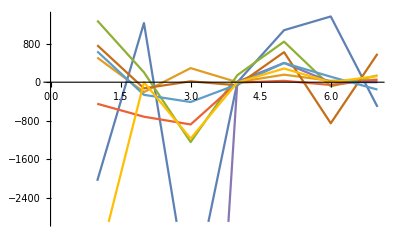

```mathematica
fn[i_]:={a1[1][[i]],a1[2][[i]],a1[3][[i]],a1[4][[i]],a1[5][[i]],a1[6][[i]],a1[7][[i]]}
ListLinePlot[{fn[1],fn[2],fn[3],fn[4],fn[5],fn[6],fn[7],fn[8]}]
```